## Simple Reservoir Model

Integrated Model - PP590
Tiago Amorim, RA: 100.675

Actual calculations start in Part 5 .

```mathematica
ClearAll;
```

## Proposed Problem

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Resolution

### Part 1 - Formulation

Assuming black-oil formulation and that there is no free gas in the reservoir, we can simplify this problem to two equations:

-Graphics-   and   -Graphics-

Applying finite differences, using the implicit form for a 1D problem and multiplying by the block volume (V):

∑_(i={i,j,k}) [T_(p,i+1/2)(Φ_(p,i+1)-Φ_(p,i))+T_(p,i-1/2)(Φ_(p,i-1)-Φ_(p,i))]^(n+1)=V_i/Δt[((ϕS_p/B_p)_i)^(n+1)-((ϕS_p/B_p)_i)^n]+(q_(p,i))^well

Where:
   p is either oil or water
   q^well is in standard conditions 
   i is one of the main flow directions (i,j,k)

The transmissibility in the x-direction is calculated between blocks (equivalent expressions for the other directions):

T_(p,i+1/2)=(λ_p(Δx Δy Δz)/Δx^2)_(i+1/2)=(k kr_p/(B_p μ_p)(Δx Δy Δz)/Δx^2)_(i+1/2)=((k A)/Δx)_(i+1/2)(1/(B_p μ_p))_(i+1/2)kr_(p,i+1/2)
((k_i A)/Δx)_(i+1/2)=(A_(i+1/2))/((x_(i+1)-x_(i+1/2))/(k_(i,i+1))+(x_(i+1/2)-x_i)/(k_(i,i)))

The first part is related to the reservoir characteristics:

((k_i A)/Δx)_(i+1/2)=(A_(i+1/2))/((x_(i+1)-x_(i+1/2))/(k_(i,i+1))+(x_(i+1/2)-x_i)/(k_(i,i)))

Where:
   x_(i+1/2)-x_i is the distance in i direction between the cell center of cells i and the interface between cells i + i+1
   A_(i+1/2) is the flow area in common between cells i and i+1

The second part is a function of pressure:

(1/(B_p μ_p))_(i+1/2)=((1/(B_p μ_p))_i+(1/(B_p μ_p))_(i+1))/2

The third part is a function of saturation and equal to the value in the upstream block (larger pressure):

kr_(p,i+1/2)=kr_(p,"upstream")

Given that for the proposed problem:
   Φ_(p,i)= P_(p,i) (no vertical displacement)
   P_o = P_w=P (no capillary pressure)
   S_o=1-S_w (no free gas)
   B_o,B_w, μ_o,μ_w, k, Δx, Δy, Δz, V are constants
   1-D problem, in the x direction
   Flow is from the injector (i=1) to the producer (i=3)
The transmissibility becomes:

T_(p,i+1/2)=(k Δy Δz)/Δx 1/(B_p μ_p)kr_(p,i)

The formulation reduces to:

[T_(p,i+1/2)(P_(i+1)-P_i)+T_(p,i-1/2)(P_(i-1)-P_i)]^(n+1)=ΔxΔyΔz/Δt ϕ/B_p[(S_(p,i))^(n+1)-(S_(p,i))^n]+(q_(p,i))^well

(k Δy Δz)/Δx(1/(B_p μ_p)[kr_(p,i)(P_(i+1)-P_i)+kr_(p,i-1)(P_(i-1)-P_i)])^(n+1)=ΔxΔyΔz/Δt ϕ/B_p[(S_(p,i))^(n+1)-(S_(p,i))^n]+(q_(p,i))^well

Which can be write in as a f(x)=0 problem:

(k Δy Δz)/Δx(1/(B_p μ_p)[kr_(p,i)P_(i+1)])^(n+1)-(k Δy Δz)/Δx(1/(B_p μ_p)[(kr_(p,i)+kr_(p,i-1))P_i])^(n+1)+(k Δy Δz)/Δx(1/(B_p μ_p)[kr_(p,i-1)P_(i-1)])^(n+1)
-ΔxΔyΔz/Δt ϕ/B_p(S_(p,i))^(n+1)+ΔxΔyΔz/Δt ϕ/B_p(S_(p,i))^n-(q_(p,i))^well=0

Where:
   (S_(p,i))^0 is known
   P_i^0 is known

Problem variables:
   (S_(p,i))^n and P_i^n, with n={1,2,...,n_(t end)}
Important to remember that:
   kr_p=f(S_p)

### Part 2 - Wells

For cell i=1 there is an injector with constant water injection rate:

(q_(w,1))^well=Q_w
(q_(o,1))^well=0

Cell i=2 has no wells:

(q_(w,2))^well=0
(q_(o,2))^well=0

Cell i=3 has a producer with constant bottom-hole pressure (p_wf):

(q_(w,3))^well=WI kr_w/(B_w μ_w)(P_wf-P_3)
(q_(o,3))^well=WI kr_o/(B_o μ_o)(P_wf-P_3)

With Δx=Δy and k_x=k_y=k:

WI=(2π k Δz)/(ln(r_e/r_w)+S)=(2π k Δz)/(ln((0.208Δx)/r_w))

### Part 3 - System of equations

Some additional constants to simplify the notation:

(k Δy Δz)/Δx 1/(B_p μ_p)=α_p

ΔxΔyΔz ϕ/B_p=β_p

WI 1/(B_p μ_p)=τ_p

Thus, the main formula becomes:

α_p[kr_(p,i)P_(i+1)]^(n+1)-α_p[(kr_(p,i)+kr_(p,i-1))P_i]^(n+1)+α_p[kr_(p,i-1)P_(i-1)]^(n+1)-β_p(S_(p,i))^(n+1)+β_p(S_(p,i))^n-(q_(p,i))^well=0

Plugging everything together:

α_o[kr_(o,1)P_2]^(n+1)-α_o[kr_(o,1)P_1]^(n+1)+β_o/Δt(S_(w,1))^(n+1)-β_o/Δt(S_(w,1))^n=0
α_w[kr_(w,1)P_2]^(n+1)-α_w[kr_(w,1)P_1]^(n+1)-β_w/Δt(S_(w,1))^(n+1)+β_w/Δt(S_(w,1))^n-Q_w=0

α_o[kr_(o,2)P_3]^(n+1)-α_o[(kr_(o,2)+kr_(o,1))P_2]^(n+1)+α_o[kr_(o,1)P_1]^(n+1)+β_o/Δt(S_(w,2))^(n+1)-β_o/Δt(S_(w,2))^n=0
α_w[kr_(w,2)P_3]^(n+1)-α_w[(kr_(w,2)+kr_(w,1))P_2]^(n+1)+α_w[kr_(w,1)P_1]^(n+1)-β_w/Δt(S_(w,2))^(n+1)+β_w/Δt(S_(w,2))^n=0

-α_o[kr_(o,2)P_3]^(n+1)+α_o[kr_(o,2)P_2]^(n+1)+β_o/Δt(S_(w,3))^(n+1)-β_o/Δt(S_(w,3))^n+τ_o[kr_(o,3)]^(n+1)P_wf-τ_o[kr_(o,3)P_3]^(n+1)=0
-α_w[kr_(w,2)P_3]^(n+1)+α_w[kr_(w,2)P_2]^(n+1)-β_w/Δt(S_(w,3))^(n+1)+β_w/Δt(S_(w,3))^n+τ_w[kr_(w,3)]^(n+1)P_wf-τ_w[kr_(w,3)P_3]^(n+1)=0

### Part 4 - Newton-Raphson

Since it is not possible to directly solve the system of equations, Newton-Raphson will be employed to search for the answer in each time-step.
Rewriting the problem in matrix form (K x = f):

(-α_o[kr_(o,1)]^(n+1) | β_o/Δt | α_o[kr_(o,1)]^(n+1) |  0 | 0  | 0 
-α_w[kr_(w,1)]^(n+1) | -β_w/Δt | α_w[kr_(w,1)]^(n+1) |  0 | 0  | 0 
α_o[kr_(o,1)]^(n+1) | 0 | -α_o[kr_(o,2)+kr_(o,1)]^(n+1) | β_o/Δt | α_o[kr_(o,2)]^(n+1) | 0 
α_w[kr_(w,1)]^(n+1) | 0 | -α_w[kr_(w,2)+kr_(w,1)]^(n+1) | -β_w/Δt | α_w[kr_(w,2)]^(n+1) | 0
0 | 0 | α_o[kr_(o,2)]^(n+1) | 0 | -α_o[kr_(o,2)]^(n+1)-τ_o[kr_(o,3)]^(n+1) | β_o/Δt
0 | 0 | α_w[kr_(w,2)]^(n+1) | 0 | -α_w[kr_(w,2)]^(n+1)-τ_w[kr_(w,3)]^(n+1) | -β_w/Δt)(P_1^(n+1)
(S_(w,1))^(n+1)
P_2^(n+1)
(S_(w,2))^(n+1)
P_3^(n+1)
(S_(w,3))^(n+1))=(β_o/Δt(S_(w,1))^n
-β_w/Δt(S_(w,1))^n+Q_w
β_o/Δt(S_(w,2))^n
-β_w/Δt(S_(w,2))^n
β_o/Δt(S_(w,3))^n-τ_o[kr_(o,3)]^(n+1)P_wf
-β_w/Δt(S_(w,3))^n-τ_w[kr_(w,3)]^(n+1)P_wf)

To use Newton-Raphson it is needed the Jacobian of R = (K x - f):

J=K+(0 | α_o (P_2^(n+1)-P_1^(n+1))(∂kr_(o,1))/(∂S_(w,1)) | 0 |  0 | 0  | 0 
0 | α_w (P_2^(n+1)-P_1^(n+1))(∂kr_(w,1))/(∂S_(w,1)) | 0 |  0 | 0  | 0 
0 | -α_o (P_2^(n+1)-P_1^(n+1))(∂kr_(o,1))/(∂S_(w,1)) | 0 | α_o (P_3^(n+1)-P_2^(n+1))(∂kr_(o,2))/(∂S_(w,2)) | 0 | 0 
0 | -α_w (P_2^(n+1)-P_1^(n+1))(∂kr_(w,1))/(∂S_(w,1)) | 0 | α_w (P_3^(n+1)-P_2^(n+1))(∂kr_(w,2))/(∂S_(w,2)) | 0 | 0
0 | 0 | 0 | -α_o (P_3^(n+1)-P_2^(n+1))(∂kr_(o,2))/(∂S_(w,2)) | 0 | -τ_o[P_3-P_wf]^(n+1)(∂kr_(o,3))/(∂S_(w,3))
0 | 0 | 0 | -α_w (P_3^(n+1)-P_2^(n+1))(∂kr_(w,2))/(∂S_(w,2)) | 0 | -τ_w[P_3-P_wf]^(n+1)(∂kr_(w,3))/(∂S_(w,3)))

Newton-Raphson algorithm (with simplified convergence controls):

Define initial Δt
   Start with the initial state (x^0)
   For i=1,...,n
      Make x_0^i=x^(i-1)
      Repeat
         Calculate f, K and J
         x_(j+1)^i=x_j^i-J^-1(Kx-f)
      Until convergence: ||K x - f|| < ϵ or j=j_max
      if Δ_t P>Δ_t P_max or Δ_t S>Δ_t S_max then
         Δt^new=Δt/2
         Repeat time-step (j--)
      else
         Δt^new=1.2 Δt
         x^i=x_(j+1)^i

### Part 5 - Relative Permeability

Actual calculations start in the next cells.

The provided plot was manually digitalized, and the curves were approximated with known Kr correlations. The major endpoints are:

```mathematica
Swc=0.10;
Swcr=0.20;
Sor=0.16;
Krwmax = 0.63;
Kromax=1.00;
```

The water curve was adjusted to the Corey formulation:

```mathematica
nw=2;
Swd=(Sw-Swcr)/(1-Swcr-Sor);
krw=Piecewise[{
{0,Sw<Swc},
{0,Sw<Swcr},
{Krwmax*Power[Swd,nw],Sw<=1-Sor},
{Krwmax+(1-Krwmax)*(Sw-1+Sor)/Sor,Sw<=1},
{1,Sw>1}
}];
dkrw=D[krw,Sw];
```

The oil curve was adjusted to the LET formulation :

```mathematica
Lo=1.7;
Eo=1.;
To=2.;
Sod=1-(Sw-Swc)/(1-Swc-Sor);
krow=Piecewise[{
{Kromax,Sw<Swc},
{Kromax*Power[Sod,Lo]/(Power[Sod,Lo]+Eo*Power[1-Sod,To]),Sw<=1-Sor},
{0,Sw<1},
{0,Sw>1}
}];
dkrow=D[krow,Sw];
```

```mathematica
Plot[{krw,krow,krw+krow,krw/(krow+krw)},{Sw,0,1},
AxesLabel->{"Sw","Kr"},
PlotLabel->"Relative Permeability",
PlotLabels->"Expressions",
GridLines->Automatic,
PlotRange->{{0,1},{0,1}}]
Plot[{D[krw,Sw]/.Sw->s, D[krow,Sw]/.Sw->s},{s,0,1},
AxesLabel->{"Sw","dKr/dSw"},
PlotLabel->"Relative Permeability Derivatives",
PlotLabels->"Expressions",
GridLines->Automatic,
PlotRange->Full]
```

-Graphics-

-Graphics-

Since Swi is defined as 0.20 in the proposed problem, it will be modified in the relative permeability parameters as well.

```mathematica
Swc=0.20;
Swcr=0.20;
Sor=0.16;
Krwmax = 0.63;
Kromax=1.00;
nw=2;
Swd=(Sw-Swcr)/(1-Swcr-Sor);
krw=Piecewise[{
{0,Sw<Swc},
{0,Sw<Swcr},
{Krwmax*Power[Swd,nw],Sw<=1-Sor},
{Krwmax+(1-Krwmax)*(Sw-1+Sor)/Sor,Sw<=1},
{1,Sw>1}
}];
Lo=1.7;
Eo=1.;
To=2.;
Sod=1-(Sw-Swc)/(1-Swc-Sor);
krow=Piecewise[{
{Kromax,Sw<Swc},
{Kromax*Power[Sod,Lo]/(Power[Sod,Lo]+Eo*Power[1-Sod,To]),Sw<=1-Sor},
{0,Sw<1},
{0,Sw>1}
}];
dkrw=D[krw,Sw];
dkrow=D[krow,Sw];
```

### Part 6 - Numerical Example

-Graphics-

-Graphics-

#### Problem description

```mathematica
Pinit=340.; (* bar *)
Swi=0.2;
k=1000; (* mD *)
ϕ=0.3;
Δx=Δy=200.; (* m *)
Δz=30.; (* m *)
Bo=1.01;
μo=130.; (* cP *)
Bw=1.;
μw=1.; (* cP *)
rw=4.*2.54/100; (* m *)
S=0.;
Qwi=-350.; (* m3/d *)
Pwf=330.; (* bar *)
tEnd=5*365.; (* days*)
```

#### Constants (with proper unit conversion)

```mathematica
αo=((k 9.869233 10^-16) Δy Δz)/Δx 1/(Bo (μo 10^-3))10^5(24 60 60);
αw=((k 9.869233 10^-16) Δy Δz)/Δx 1/(Bw (μw 10^-3))10^5(24 60 60);
```

```mathematica
βo=Δx Δy Δz ϕ/Bo;
βw=Δx Δy Δz ϕ/Bw;
```

```mathematica
WI=(2π (k 9.869233 10^-16) Δz)/(Log[(0.208Δx)/rw]+S);
```

```mathematica
τo=WI 1/(Bo (μo 10^-3))10^5(24 60 60);
τw=WI 1/(Bw (μw 10^-3))10^5(24 60 60);
```

#### Some Quantities

```mathematica
Print["Pore volume: ",Δx Δy Δz ϕ," m3"]
```

Pore volume: 360000. m3

```mathematica
Print["Time do inject 1% of pore volume: ",-0.01*Δx Δy Δz ϕ/Qwi," days"]
```

Time do inject 1% of pore volume: 10.2857 days

```mathematica
Print["Initial potential producer flow rate: ",τo(Pinit-Pwf) krow/.Sw->Swi," m3/d"]
```

Initial potential producer flow rate: 20.3522 m3/d

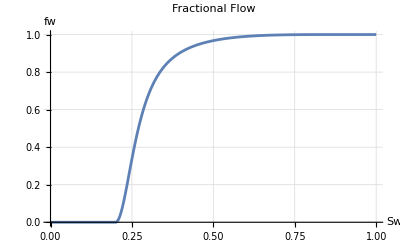

```mathematica
fw=Piecewise[{
{0,Sw<=Swi},
{1/(1+(krow/(Bo μo))/(krw/(Bw μw))),True}
}];
Plot[{fw/.Sw->s},{s,0,1},
AxesLabel->{"Sw","fw"},
PlotLabel->"Fractional Flow",
GridLines->Automatic,
PlotRange->Full]
```

#### Main functions

```mathematica
buildK[x_,Δt_]:=Block[{Sw,kro1,kro2,kro3,krw1,krw2,krw3,K},
kro1 = krow/.Sw->x[[2]];
krw1 = krw/.Sw->x[[2]];
kro2 = krow/.Sw->x[[4]];
krw2 = krw/.Sw->x[[4]];
kro3 = krow/.Sw->x[[6]];
krw3 = krw/.Sw->x[[6]];
K={{-αo kro1,βo/Δt,αo kro1,0,0,0}};
K=ArrayFlatten[{{K},{{{-αw krw1,-βw/Δt,αw krw1,0,0,0}}}}];
K=ArrayFlatten[{{K},{{{αo kro1,0,-αo(kro2+kro1),βo/Δt,αo kro2,0}}}}];
K=ArrayFlatten[{{K},{{{αw krw1,0,-αw(krw2+krw1),-βw/Δt,αw krw2,0}}}}];
K=ArrayFlatten[{{K},{{{0,0,αo kro2,0,-αo kro2-τo kro3,βo/Δt}}}}];
K=ArrayFlatten[{{K},{{{0,0,αw krw2,0,-αw krw2-τw krw3,-βw/Δt}}}}];
K]
```

```mathematica
buildF[xNew_,xOld_,Δt_]:=Block[{Sw,F,kro3,krw3},
kro3 = krow/.Sw->xNew[[6]];
krw3 = krw/.Sw->xNew[[6]];
F={0,0,0,0,0,0};
F[[1]] = βo/Δt xOld[[2]];
F[[2]] = -βw/Δt xOld[[2]]+Qwi;
F[[3]] = βo/Δt xOld[[4]];
F[[4]] = -βw/Δt xOld[[4]];
F[[5]] = βo/Δt xOld[[6]]-τo kro3 Pwf;
F[[6]] = -βw/Δt xOld[[6]]-τw krw3 Pwf;
F]
```

```mathematica
buildJ[x_,Δt_]:=Block[{Sw,dkro1,dkro2,dkro3,dkrw1,dkrw2,dkrw3,J},
dkro1 = dkrow/.Sw->x[[2]];
dkrw1 = dkrw/.Sw->x[[2]];
dkro2 = dkrow/.Sw->x[[4]];
dkrw2 = dkrw/.Sw->x[[4]];
dkro3 = dkrow/.Sw->x[[6]];
dkrw3 = dkrw/.Sw->x[[6]];
J=buildK[x,Δt];

J[[1]][[2]] += αo (x[[3]]-x[[1]])dkro1;
J[[2]][[2]] += αw (x[[3]]-x[[1]])dkrw1;

J[[3]][[2]] += -αo (x[[3]]-x[[1]])dkro1;
J[[4]][[2]] += -αw (x[[3]]-x[[1]])dkrw1;
J[[3]][[4]] += αo (x[[5]]-x[[3]])dkro2;
J[[4]][[4]] += αw (x[[5]]-x[[3]])dkrw2;

J[[5]][[4]] += -αo (x[[5]]-x[[3]])dkro2;
J[[6]][[4]] += -αw (x[[5]]-x[[3]])dkrw2;
J[[5]][[6]] += -τo (x[[5]]-Pwf)dkro3;
J[[6]][[6]] += -τw (x[[5]]-Pwf)dkrw3;
J]
```

```mathematica
buildR[x_,xOld_,Δt_,verbose_]:=Block[{K,F,R},
K = buildK[x,Δt];
F = buildF[x,xOld,Δt];
R=Dot[K,x] - F;
If[verbose,
Print["X=",MatrixForm[x]];
Print["K=",MatrixForm[K]];
Print["F=",MatrixForm[F]];
Print["R=",MatrixForm[R]];
];
R]
```

```mathematica
solveNextX[xOld_,Δt_,verbose_]:=Block[{K,F,J,R,x, dx,MaxDeltaP,MaxDeltaS},
x = xOld;
n=1;
If[False,Print["Initial value"]];
R = buildR[x,xOld,Δt,False];
While[n<=10 &&Norm[R]>10^-6,
J = buildJ[x,Δt];
dx=LinearSolve[J,-R];
x+=dx;
If[False,Print["Iteration ",n]];
R = buildR[x,xOld,Δt,False];
n++];
dx=x-xOld;
MaxDeltaP=Max[Abs[dx[[1]]],Abs[dx[[3]]],Abs[dx[[5]]]];
MaxDeltaS=Max[Abs[dx[[2]]],Abs[dx[[4]]],Abs[dx[[6]]]];
If[verbose,Print["   iterations: ",n,"; ||R||=",Norm[R]," MaxΔP=",MaxDeltaP ," MaxΔS=",MaxDeltaS ]];
{x,dx}
]
```

```mathematica
checkConvergence[ΔPmax_,ΔSmax_,dx_]:=Block[{MaxDeltaP,MaxDeltaS,ok},
MaxDeltaP=Max[Abs[dx[[1]]],Abs[dx[[3]]],Abs[dx[[5]]]];
MaxDeltaS=Max[Abs[dx[[2]]],Abs[dx[[4]]],Abs[dx[[6]]]];
ok = (MaxDeltaP <ΔPmax) && (MaxDeltaS <ΔSmax);
ok
]
```

```mathematica
runSim[xInit_,ΔPmax_,ΔSmax_,Δtmax_,ΔtInit_,verbose_]:=Block[{x,Δt,t,xLast,xNew,dx, dxNew,i},
Δt=ΔtInit;
t={0};
x={xInit};
dx={{0,0,0,0,0,0}};
xLast = xInit;
For[i=0,t[[i+1]]<tEnd,i++,
If[verbose,Print["Time-step: ",i+1,",  Time: ",t[[i+1]]+Δt,",  Δt: ",Δt," days"]];
{xNew,dxNew}=solveNextX[xLast,Δt,verbose];
(* In this incompressible system the first dP is very high, an so it will be ignored in the 1st time-step. *)
If[checkConvergence[If[Length[t]>1,ΔPmax,10^6],ΔSmax,dxNew],
xLast=xNew;
AppendTo[t,t[[i+1]]+Δt];
AppendTo[x,xNew];
AppendTo[dx,dxNew];
Δt=Min[1.2 Δt,Δtmax,tEnd-t[[i+2]]];
,
Δt=0.5 Δt;
If[verbose,Print["Convergence criteria failed. New Δt: ",Δt," days"]];
i--;
];
];
{t,x,dx}
]
```

```mathematica
postProcess[t_,x_,dx_]:=Block[{i,n,P1,P2,P3,S1,S2,S3,t2,dP1,dP2,dP3,dS1,dS2,dS3,kro3,krw3,Qop,Qwp,Qlp,Qwiv,Wcut},

Print[ListLinePlot[{Transpose[{t,Join[{0},Differences[t]]}]},
AxesLabel->{"Time [days]","Δt [days]"},
PlotLabel->"Time-Step Size",
GridLines->Automatic,
PlotRange->Full]];

n=Length[t];
P1=Table[x[[i]][[1]],{i, n}];
P2=Table[x[[i]][[3]],{i,n}];
P3=Table[x[[i]][[5]],{i,n}];
S1=Table[x[[i]][[2]],{i,n}];
S2=Table[x[[i]][[4]],{i,n}];
S3=Table[x[[i]][[6]],{i,n}];

Print[ListLinePlot[{Transpose[{t,P1}],Transpose[{t,P2}],Transpose[{t,P3}]},
AxesLabel->{"Time [days]","Pressure [bar]"},
PlotLabel->"Block Pressures",
PlotLabels->{"P1","P2","P3"},
GridLines->Automatic,
PlotRange->Full]];

Print[ListLinePlot[{Transpose[{t,S1*100}],Transpose[{t,S2*100}],Transpose[{t,S3*100}]},
AxesLabel->{"Time [days]","Saturation [%]"},
PlotLabel->"Block Saturarions",
PlotLabels->{"S1","S2","S3"},
GridLines->Automatic,
PlotRange->Full]];

(* In this incompressible system the first dP is very high, an so it will be ignored in the 1st time-step. *)
t2=Take[t,-(n-2)];
dP1=Table[dx[[i+2]][[1]],{i, n-2}];
dP2=Table[dx[[i+2]][[3]],{i,n-2}];
dP3=Table[dx[[i+2]][[5]],{i,n-2}];
dS1=Table[dx[[i+2]][[2]],{i,n-2}];
dS2=Table[dx[[i+2]][[4]],{i,n-2}];
dS3=Table[dx[[i+2]][[6]],{i,n-2}];

Print[ListLinePlot[{Transpose[{t2,dP1}],Transpose[{t2,dP2}],Transpose[{t2,dP3}]},
AxesLabel->{"Time [days]","ΔPressure [bar]"},
PlotLabel->"Block Delta Pressures",
PlotLabels->{"ΔP1","ΔP2","ΔP3"},
GridLines->Automatic,
PlotRange->Full]];

Print[ListLinePlot[{Transpose[{t2,dS1*100}],Transpose[{t2,dS2*100}],Transpose[{t2,dS3*100}]},
AxesLabel->{"Time [days]","ΔSaturation [%]"},
PlotLabel->"Block Delta Saturarions",
PlotLabels->{"ΔS1","ΔS2","ΔS3"},
GridLines->Automatic,
PlotRange->Full]];

kro3 = Table[krow/.Sw->S3[[i]],{i,n}];
krw3 = Table[krw/.Sw->S3[[i]],{i, n}];
Qop=Table[τo kro3[[i]] (P3[[i]]-Pwf),{i, n}];
Qwp=Table[τw krw3[[i]] (P3[[i]]-Pwf),{i, n}];
Qlp=Qop+Qwp;
Qwiv=Table[-Qwi,{i, n}];
Wcut=Qwp/(Qop+Qwp);

colors={Green,Blue,Black,Purple};
Print[ListLinePlot[{Transpose[{t,Qop}],Transpose[{t,Qwp}],Transpose[{t,Qlp}],Transpose[{t,Qwiv}]},
AxesLabel->{"Time [days]","Liquid Flow [m3/d]"},
PlotLabel->"Well Rates",
PlotLabels->{"Qop","Qwp","Qlp","Qwi"},
PlotStyle->colors,
GridLines->Automatic,
PlotRange->Full]];

Print[ListLinePlot[{Transpose[{t,Wcut*100}]},
AxesLabel->{"Time [days]","Water-cut [%]"},
PlotLabel->"Water Cut",
GridLines->Automatic,
PlotRange->Full]];
]
```

#### Simulation

```mathematica
xInit={Pinit,Swi,Pinit,Swi,Pinit,Swi};
```

```mathematica
{t,x,dx}=runSim[xInit,1,0.005, 10,1,True];
```

Time-step: 1,  Time: 1,  Δt: 1 days

iterations: 3; ||R||=8.73573×10^-9 MaxΔP=515.968 MaxΔS=0.000972039

Time-step: 2,  Time: 2.2,  Δt: 1.2 days

iterations: 3; ||R||=4.16155×10^-8 MaxΔP=0.127186 MaxΔS=0.0011656

Time-step: 3,  Time: 3.64,  Δt: 1.44 days

iterations: 3; ||R||=1.6075×10^-7 MaxΔP=0.277283 MaxΔS=0.00139651

Time-step: 4,  Time: 5.368,  Δt: 1.728 days

iterations: 3; ||R||=5.55346×10^-7 MaxΔP=0.50891 MaxΔS=0.00167095

Time-step: 5,  Time: 7.4416,  Δt: 2.0736 days

iterations: 4; ||R||=0. MaxΔP=0.855951 MaxΔS=0.00199531

Time-step: 6,  Time: 9.92992,  Δt: 2.48832 days

iterations: 4; ||R||=6.30116×10^-12 MaxΔP=1.36087 MaxΔS=0.00237563

Convergence criteria failed. New Δt: 1.24416 days

Time-step: 6,  Time: 8.68576,  Δt: 1.24416 days

iterations: 3; ||R||=1.4414×10^-7 MaxΔP=0.63773 MaxΔS=0.0011928

Time-step: 7,  Time: 10.1788,  Δt: 1.49299 days

iterations: 3; ||R||=3.90033×10^-7 MaxΔP=0.881479 MaxΔS=0.00142407

Time-step: 8,  Time: 11.9703,  Δt: 1.79159 days

iterations: 4; ||R||=1.02898×10^-11 MaxΔP=1.21566 MaxΔS=0.00169683

Convergence criteria failed. New Δt: 0.895795 days

Time-step: 8,  Time: 11.0745,  Δt: 0.895795 days

iterations: 3; ||R||=3.02933×10^-8 MaxΔP=0.587985 MaxΔS=0.000851526

Time-step: 9,  Time: 12.1495,  Δt: 1.07495 days

iterations: 3; ||R||=7.7401×10^-8 MaxΔP=0.760643 MaxΔS=0.00101731

Time-step: 10,  Time: 13.4394,  Δt: 1.28995 days

iterations: 3; ||R||=1.95252×10^-7 MaxΔP=0.98811 MaxΔS=0.00121371

Time-step: 11,  Time: 14.9874,  Δt: 1.54793 days

iterations: 3; ||R||=4.82427×10^-7 MaxΔP=1.2871 MaxΔS=0.00144543

Convergence criteria failed. New Δt: 0.773967 days

Time-step: 11,  Time: 14.2134,  Δt: 0.773967 days

iterations: 3; ||R||=1.46887×10^-8 MaxΔP=0.631342 MaxΔS=0.000725523

Time-step: 12,  Time: 15.1422,  Δt: 0.92876 days

iterations: 3; ||R||=3.62668×10^-8 MaxΔP=0.792799 MaxΔS=0.000866553

Time-step: 13,  Time: 16.2567,  Δt: 1.11451 days

iterations: 3; ||R||=8.82762×10^-8 MaxΔP=0.99926 MaxΔS=0.0010337

Time-step: 14,  Time: 17.5941,  Δt: 1.33742 days

iterations: 3; ||R||=2.10981×10^-7 MaxΔP=1.26326 MaxΔS=0.0012311

Convergence criteria failed. New Δt: 0.668708 days

Time-step: 14,  Time: 16.9254,  Δt: 0.668708 days

iterations: 3; ||R||=6.53601×10^-9 MaxΔP=0.62429 MaxΔS=0.000617912

Time-step: 15,  Time: 17.7278,  Δt: 0.802449 days

iterations: 3; ||R||=1.58609×10^-8 MaxΔP=0.771363 MaxΔS=0.00073807

Time-step: 16,  Time: 18.6908,  Δt: 0.962939 days

iterations: 3; ||R||=3.78895×10^-8 MaxΔP=0.955812 MaxΔS=0.000880595

Time-step: 17,  Time: 19.8463,  Δt: 1.15553 days

iterations: 3; ||R||=8.89701×10^-8 MaxΔP=1.18732 MaxΔS=0.00104913

Convergence criteria failed. New Δt: 0.577763 days

Time-step: 17,  Time: 19.2685,  Δt: 0.577763 days

iterations: 3; ||R||=2.77854×10^-9 MaxΔP=0.589323 MaxΔS=0.000526474

Time-step: 18,  Time: 19.9619,  Δt: 0.693316 days

iterations: 3; ||R||=6.69979×10^-9 MaxΔP=0.721148 MaxΔS=0.000629005

Time-step: 19,  Time: 20.7938,  Δt: 0.831979 days

iterations: 3; ||R||=1.58397×10^-8 MaxΔP=0.884338 MaxΔS=0.000750741

Time-step: 20,  Time: 21.7922,  Δt: 0.998375 days

iterations: 3; ||R||=3.69198×10^-8 MaxΔP=1.08657 MaxΔS=0.000894897

Convergence criteria failed. New Δt: 0.499187 days

Time-step: 20,  Time: 21.293,  Δt: 0.499187 days

iterations: 3; ||R||=1.15319×10^-9 MaxΔP=0.540756 MaxΔS=0.000448953

Time-step: 21,  Time: 21.8921,  Δt: 0.599025 days

iterations: 3; ||R||=2.76831×10^-9 MaxΔP=0.657684 MaxΔS=0.000536568

Time-step: 22,  Time: 22.6109,  Δt: 0.71883 days

iterations: 3; ||R||=6.56608×10^-9 MaxΔP=0.801154 MaxΔS=0.000640702

Time-step: 23,  Time: 23.4735,  Δt: 0.862596 days

iterations: 3; ||R||=1.52426×10^-8 MaxΔP=0.977375 MaxΔS=0.00076419

Time-step: 24,  Time: 24.5086,  Δt: 1.03512 days

iterations: 3; ||R||=3.46954×10^-8 MaxΔP=1.19387 MaxΔS=0.000910213

Convergence criteria failed. New Δt: 0.517558 days

Time-step: 24,  Time: 23.991,  Δt: 0.517558 days

iterations: 3; ||R||=1.11396×10^-9 MaxΔP=0.595174 MaxΔS=0.000456815

Time-step: 25,  Time: 24.6121,  Δt: 0.621069 days

iterations: 3; ||R||=2.59371×10^-9 MaxΔP=0.721409 MaxΔS=0.000545707

Time-step: 26,  Time: 25.3574,  Δt: 0.745283 days

iterations: 3; ||R||=6.00989×10^-9 MaxΔP=0.875343 MaxΔS=0.000651253

Time-step: 27,  Time: 26.2517,  Δt: 0.89434 days

iterations: 3; ||R||=1.37084×10^-8 MaxΔP=1.06311 MaxΔS=0.000776268

Convergence criteria failed. New Δt: 0.44717 days

Time-step: 27,  Time: 25.8046,  Δt: 0.44717 days

iterations: 3; ||R||=4.3266×10^-10 MaxΔP=0.530675 MaxΔS=0.000389445

Time-step: 28,  Time: 26.3412,  Δt: 0.536604 days

iterations: 3; ||R||=1.00987×10^-9 MaxΔP=0.641161 MaxΔS=0.000465439

Time-step: 29,  Time: 26.9851,  Δt: 0.643924 days

iterations: 3; ||R||=2.39784×10^-9 MaxΔP=0.775231 MaxΔS=0.00055578

Time-step: 30,  Time: 27.7578,  Δt: 0.772709 days

iterations: 3; ||R||=5.46463×10^-9 MaxΔP=0.937969 MaxΔS=0.00066295

Time-step: 31,  Time: 28.685,  Δt: 0.927251 days

iterations: 3; ||R||=1.21645×10^-8 MaxΔP=1.13546 MaxΔS=0.000789757

Convergence criteria failed. New Δt: 0.463626 days

Time-step: 31,  Time: 28.2214,  Δt: 0.463626 days

iterations: 3; ||R||=3.99052×10^-10 MaxΔP=0.567338 MaxΔS=0.000396325

Time-step: 32,  Time: 28.7778,  Δt: 0.556351 days

iterations: 3; ||R||=8.85517×10^-10 MaxΔP=0.684145 MaxΔS=0.000473499

Time-step: 33,  Time: 29.4454,  Δt: 0.667621 days

iterations: 3; ||R||=2.07914×10^-9 MaxΔP=0.825366 MaxΔS=0.000565175

Time-step: 34,  Time: 30.2465,  Δt: 0.801145 days

iterations: 3; ||R||=4.64133×10^-9 MaxΔP=0.996074 MaxΔS=0.000673835

Time-step: 35,  Time: 31.2079,  Δt: 0.961374 days

iterations: 3; ||R||=1.01161×10^-8 MaxΔP=1.20227 MaxΔS=0.000802274

Convergence criteria failed. New Δt: 0.480687 days

Time-step: 35,  Time: 30.7272,  Δt: 0.480687 days

iterations: 3; ||R||=3.29272×10^-10 MaxΔP=0.601245 MaxΔS=0.000402718

Time-step: 36,  Time: 31.304,  Δt: 0.576824 days

iterations: 3; ||R||=7.31948×10^-10 MaxΔP=0.723791 MaxΔS=0.000480976

Time-step: 37,  Time: 31.9962,  Δt: 0.692189 days

iterations: 3; ||R||=1.67739×10^-9 MaxΔP=0.871465 MaxΔS=0.000573874

Time-step: 38,  Time: 32.8269,  Δt: 0.830627 days

iterations: 3; ||R||=3.68402×10^-9 MaxΔP=1.04931 MaxΔS=0.00068389

Convergence criteria failed. New Δt: 0.415314 days

Time-step: 38,  Time: 32.4116,  Δt: 0.415314 days

iterations: 3; ||R||=1.54003×10^-10 MaxΔP=0.524964 MaxΔS=0.000343133

Time-step: 39,  Time: 32.9099,  Δt: 0.498376 days

iterations: 3; ||R||=2.50361×10^-10 MaxΔP=0.631111 MaxΔS=0.000410043

Time-step: 40,  Time: 33.508,  Δt: 0.598052 days

iterations: 3; ||R||=5.97161×10^-10 MaxΔP=0.758773 MaxΔS=0.000489577

Time-step: 41,  Time: 34.2256,  Δt: 0.717662 days

iterations: 3; ||R||=1.35872×10^-9 MaxΔP=0.912233 MaxΔS=0.000583928

Time-step: 42,  Time: 35.0868,  Δt: 0.861194 days

iterations: 3; ||R||=2.8815×10^-9 MaxΔP=1.09654 MaxΔS=0.000695581

Convergence criteria failed. New Δt: 0.430597 days

Time-step: 42,  Time: 34.6562,  Δt: 0.430597 days

iterations: 3; ||R||=1.16415×10^-10 MaxΔP=0.548869 MaxΔS=0.000349072

Time-step: 43,  Time: 35.173,  Δt: 0.516717 days

iterations: 3; ||R||=2.05795×10^-10 MaxΔP=0.659191 MaxΔS=0.000417035

Time-step: 44,  Time: 35.793,  Δt: 0.62006 days

iterations: 3; ||R||=4.9562×10^-10 MaxΔP=0.791616 MaxΔS=0.000497779

Time-step: 45,  Time: 36.5371,  Δt: 0.744072 days

iterations: 3; ||R||=9.9816×10^-10 MaxΔP=0.950451 MaxΔS=0.000593504

Time-step: 46,  Time: 37.43,  Δt: 0.892886 days

iterations: 3; ||R||=2.06898×10^-9 MaxΔP=1.14074 MaxΔS=0.000706701

Convergence criteria failed. New Δt: 0.446443 days

Time-step: 46,  Time: 36.9835,  Δt: 0.446443 days

iterations: 3; ||R||=9.20344×10^-11 MaxΔP=0.571252 MaxΔS=0.000354723

Time-step: 47,  Time: 37.5193,  Δt: 0.535732 days

iterations: 3; ||R||=1.90847×10^-10 MaxΔP=0.685464 MaxΔS=0.000423684

Time-step: 48,  Time: 38.1621,  Δt: 0.642878 days

iterations: 3; ||R||=3.0972×10^-10 MaxΔP=0.822321 MaxΔS=0.00050557

Time-step: 49,  Time: 38.9336,  Δt: 0.771454 days

iterations: 3; ||R||=6.6923×10^-10 MaxΔP=0.986158 MaxΔS=0.000602591

Time-step: 50,  Time: 39.8593,  Δt: 0.925744 days

iterations: 3; ||R||=1.29716×10^-9 MaxΔP=1.18203 MaxΔS=0.000717238

Convergence criteria failed. New Δt: 0.462872 days

Time-step: 50,  Time: 39.3965,  Δt: 0.462872 days

iterations: 3; ||R||=6.50781×10^-11 MaxΔP=0.592156 MaxΔS=0.000360082

Time-step: 51,  Time: 39.9519,  Δt: 0.555447 days

iterations: 3; ||R||=9.76172×10^-11 MaxΔP=0.709996 MaxΔS=0.000429984

Time-step: 52,  Time: 40.6184,  Δt: 0.666536 days

iterations: 3; ||R||=1.75228×10^-10 MaxΔP=0.850996 MaxΔS=0.000512946

Time-step: 53,  Time: 41.4183,  Δt: 0.799843 days

iterations: 3; ||R||=3.61169×10^-10 MaxΔP=1.01952 MaxΔS=0.000611183

Convergence criteria failed. New Δt: 0.399922 days

Time-step: 53,  Time: 41.0184,  Δt: 0.399922 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.510685 MaxΔS=0.000306676

Time-step: 54,  Time: 41.4983,  Δt: 0.479906 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.612163 MaxΔS=0.000366445

Time-step: 55,  Time: 42.0742,  Δt: 0.575887 days

iterations: 3; ||R||=4.82632×10^-11 MaxΔP=0.73357 MaxΔS=0.000437486

Time-step: 56,  Time: 42.7652,  Δt: 0.691065 days

iterations: 3; ||R||=8.48515×10^-11 MaxΔP=0.878685 MaxΔS=0.000521759

Time-step: 57,  Time: 43.5945,  Δt: 0.829277 days

iterations: 3; ||R||=1.56052×10^-10 MaxΔP=1.05193 MaxΔS=0.000621496

Convergence criteria failed. New Δt: 0.414639 days

Time-step: 57,  Time: 43.1799,  Δt: 0.414639 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.527029 MaxΔS=0.000311898

Time-step: 58,  Time: 43.6774,  Δt: 0.497566 days

iterations: 3; ||R||=9.20344×10^-11 MaxΔP=0.631489 MaxΔS=0.000372616

Time-step: 59,  Time: 44.2745,  Δt: 0.59708 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.756364 MaxΔS=0.000444758

Time-step: 60,  Time: 44.991,  Δt: 0.716496 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.905495 MaxΔS=0.000530298

Time-step: 61,  Time: 45.8508,  Δt: 0.859795 days

iterations: 3; ||R||=3.85007×10^-11 MaxΔP=1.08337 MaxΔS=0.000631479

Convergence criteria failed. New Δt: 0.429897 days

Time-step: 61,  Time: 45.4209,  Δt: 0.429897 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.542874 MaxΔS=0.000316955

Time-step: 62,  Time: 45.9368,  Δt: 0.515877 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.650248 MaxΔS=0.00037859

Time-step: 63,  Time: 46.5558,  Δt: 0.619052 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.778528 MaxΔS=0.000451794

Time-step: 64,  Time: 47.2987,  Δt: 0.742863 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.931626 MaxΔS=0.000538555

Time-step: 65,  Time: 48.1901,  Δt: 0.891435 days

iterations: 3; ||R||=6.97885×10^-11 MaxΔP=1.11412 MaxΔS=0.000641126

Convergence criteria failed. New Δt: 0.445718 days

Time-step: 65,  Time: 47.7444,  Δt: 0.445718 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.558346 MaxΔS=0.000321843

Time-step: 66,  Time: 48.2793,  Δt: 0.534861 days

iterations: 3; ||R||=6.50781×10^-11 MaxΔP=0.668602 MaxΔS=0.000384363

Time-step: 67,  Time: 48.9211,  Δt: 0.641833 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.800266 MaxΔS=0.00045859

Time-step: 68,  Time: 49.6913,  Δt: 0.7702 days

iterations: 3; ||R||=5.63593×10^-11 MaxΔP=0.957335 MaxΔS=0.000546526

Time-step: 69,  Time: 50.6156,  Δt: 0.92424 days

iterations: 3; ||R||=1.4332×10^-10 MaxΔP=1.14448 MaxΔS=0.000650435

Convergence criteria failed. New Δt: 0.46212 days

Time-step: 69,  Time: 50.1534,  Δt: 0.46212 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.573608 MaxΔS=0.00032656

Time-step: 70,  Time: 50.708,  Δt: 0.554544 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.686751 MaxΔS=0.000389932

Time-step: 71,  Time: 51.3734,  Δt: 0.665453 days

iterations: 3; ||R||=6.66853×10^-11 MaxΔP=0.821829 MaxΔS=0.000465144

Time-step: 72,  Time: 52.172,  Δt: 0.798543 days

iterations: 3; ||R||=9.65265×10^-11 MaxΔP=0.982936 MaxΔS=0.00055421

Time-step: 73,  Time: 53.1302,  Δt: 0.958252 days

iterations: 3; ||R||=3.10403×10^-10 MaxΔP=1.17487 MaxΔS=0.000659404

Convergence criteria failed. New Δt: 0.479126 days

Time-step: 73,  Time: 52.6511,  Δt: 0.479126 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.588852 MaxΔS=0.000331107

Time-step: 74,  Time: 53.226,  Δt: 0.574951 days

iterations: 3; ||R||=3.85007×10^-11 MaxΔP=0.704932 MaxΔS=0.000395299

Time-step: 75,  Time: 53.916,  Δt: 0.689942 days

iterations: 3; ||R||=7.5614×10^-11 MaxΔP=0.843506 MaxΔS=0.000471457

Time-step: 76,  Time: 54.7439,  Δt: 0.82793 days

iterations: 3; ||R||=1.97392×10^-10 MaxΔP=1.00878 MaxΔS=0.000561609

Convergence criteria failed. New Δt: 0.413965 days

Time-step: 76,  Time: 54.33,  Δt: 0.413965 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.505418 MaxΔS=0.000281835

Time-step: 77,  Time: 54.8267,  Δt: 0.496758 days

iterations: 3; ||R||=6.50781×10^-11 MaxΔP=0.605264 MaxΔS=0.000336714

Time-step: 78,  Time: 55.4228,  Δt: 0.596109 days

iterations: 3; ||R||=6.82545×10^-11 MaxΔP=0.724555 MaxΔS=0.000401928

Time-step: 79,  Time: 56.1382,  Δt: 0.715331 days

iterations: 3; ||R||=1.35731×10^-10 MaxΔP=0.866972 MaxΔS=0.000479275

Time-step: 80,  Time: 56.9966,  Δt: 0.858398 days

iterations: 3; ||R||=3.60288×10^-10 MaxΔP=1.03685 MaxΔS=0.000570797

Convergence criteria failed. New Δt: 0.429199 days

Time-step: 80,  Time: 56.5674,  Δt: 0.429199 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.51947 MaxΔS=0.000286477

Time-step: 81,  Time: 57.0824,  Δt: 0.515039 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.622098 MaxΔS=0.000342215

Time-step: 82,  Time: 57.7004,  Δt: 0.618046 days

iterations: 3; ||R||=8.60903×10^-11 MaxΔP=0.744727 MaxΔS=0.000408432

Time-step: 83,  Time: 58.4421,  Δt: 0.741656 days

iterations: 3; ||R||=2.22125×10^-10 MaxΔP=0.891153 MaxΔS=0.000486941

Time-step: 84,  Time: 59.3321,  Δt: 0.889987 days

iterations: 3; ||R||=5.80255×10^-10 MaxΔP=1.06586 MaxΔS=0.000579803

Convergence criteria failed. New Δt: 0.444993 days

Time-step: 84,  Time: 58.8871,  Δt: 0.444993 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.533979 MaxΔS=0.000291028

Time-step: 85,  Time: 59.4211,  Δt: 0.533992 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.63951 MaxΔS=0.000347607

Time-step: 86,  Time: 60.0619,  Δt: 0.64079 days

iterations: 3; ||R||=1.47686×10^-10 MaxΔP=0.765634 MaxΔS=0.000414805

Time-step: 87,  Time: 60.8308,  Δt: 0.768949 days

iterations: 3; ||R||=3.27337×10^-10 MaxΔP=0.916275 MaxΔS=0.000494452

Time-step: 88,  Time: 61.7536,  Δt: 0.922738 days

iterations: 3; ||R||=8.60903×10^-10 MaxΔP=1.09608 MaxΔS=0.000588625

Convergence criteria failed. New Δt: 0.461369 days

Time-step: 88,  Time: 61.2922,  Δt: 0.461369 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.54908 MaxΔS=0.000295486

Time-step: 89,  Time: 61.8458,  Δt: 0.553643 days

iterations: 3; ||R||=1.23477×10^-10 MaxΔP=0.657663 MaxΔS=0.000352888

Time-step: 90,  Time: 62.5102,  Δt: 0.664372 days

iterations: 3; ||R||=2.08859×10^-10 MaxΔP=0.78747 MaxΔS=0.000421046

Time-step: 91,  Time: 63.3074,  Δt: 0.797246 days

iterations: 3; ||R||=4.74892×10^-10 MaxΔP=0.94257 MaxΔS=0.000501806

Time-step: 92,  Time: 64.2641,  Δt: 0.956695 days

iterations: 3; ||R||=1.19335×10^-9 MaxΔP=1.12779 MaxΔS=0.00059726

Convergence criteria failed. New Δt: 0.478347 days

Time-step: 92,  Time: 63.7858,  Δt: 0.478347 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.564912 MaxΔS=0.00029985

Time-step: 93,  Time: 64.3598,  Δt: 0.574017 days

iterations: 3; ||R||=1.01863×10^-10 MaxΔP=0.676719 MaxΔS=0.000358058

Time-step: 94,  Time: 65.0486,  Δt: 0.68882 days

iterations: 3; ||R||=2.57861×10^-10 MaxΔP=0.81043 MaxΔS=0.000427154

Time-step: 95,  Time: 65.8752,  Δt: 0.826584 days

iterations: 3; ||R||=6.51269×10^-10 MaxΔP=0.970265 MaxΔS=0.000509001

Time-step: 96,  Time: 66.8671,  Δt: 0.991901 days

iterations: 3; ||R||=1.63597×10^-9 MaxΔP=1.16125 MaxΔS=0.000605708

Convergence criteria failed. New Δt: 0.495951 days

Time-step: 96,  Time: 66.3712,  Δt: 0.495951 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.581608 MaxΔS=0.000304121

Time-step: 97,  Time: 66.9663,  Δt: 0.595141 days

iterations: 3; ||R||=1.4332×10^-10 MaxΔP=0.696838 MaxΔS=0.000363115

Time-step: 98,  Time: 67.6805,  Δt: 0.714169 days

iterations: 3; ||R||=3.33744×10^-10 MaxΔP=0.834696 MaxΔS=0.000433129

Time-step: 99,  Time: 68.5375,  Δt: 0.857003 days

iterations: 3; ||R||=8.42504×10^-10 MaxΔP=0.99957 MaxΔS=0.00051604

Time-step: 100,  Time: 69.5659,  Δt: 1.0284 days

iterations: 3; ||R||=2.17618×10^-9 MaxΔP=1.19669 MaxΔS=0.00061397

Convergence criteria failed. New Δt: 0.514202 days

Time-step: 100,  Time: 69.0517,  Δt: 0.514202 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.599291 MaxΔS=0.000308297

Time-step: 101,  Time: 69.6687,  Δt: 0.617042 days

iterations: 3; ||R||=1.94691×10^-10 MaxΔP=0.718159 MaxΔS=0.000368061

Time-step: 102,  Time: 70.4092,  Δt: 0.74045 days

iterations: 3; ||R||=4.29466×10^-10 MaxΔP=0.86043 MaxΔS=0.000438972

Time-step: 103,  Time: 71.2977,  Δt: 0.88854 days

iterations: 3; ||R||=1.10413×10^-9 MaxΔP=1.03067 MaxΔS=0.000522922

Convergence criteria failed. New Δt: 0.44427 days

Time-step: 103,  Time: 70.8534,  Δt: 0.44427 days

iterations: 3; ||R||=8.73115×10^-11 MaxΔP=0.51599 MaxΔS=0.000262417

Time-step: 104,  Time: 71.3866,  Δt: 0.533124 days

iterations: 3; ||R||=1.00819×10^-10 MaxΔP=0.618531 MaxΔS=0.00031352

Time-step: 105,  Time: 72.0263,  Δt: 0.639749 days

iterations: 3; ||R||=2.03206×10^-10 MaxΔP=0.741333 MaxΔS=0.000374252

Time-step: 106,  Time: 72.794,  Δt: 0.767699 days

iterations: 3; ||R||=5.49708×10^-10 MaxΔP=0.888362 MaxΔS=0.000446293

Time-step: 107,  Time: 73.7153,  Δt: 0.921239 days

iterations: 3; ||R||=1.4059×10^-9 MaxΔP=1.06436 MaxΔS=0.000531555

Convergence criteria failed. New Δt: 0.460619 days

Time-step: 107,  Time: 73.2546,  Δt: 0.460619 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.532819 MaxΔS=0.000266772

Time-step: 108,  Time: 73.8074,  Δt: 0.552743 days

iterations: 3; ||R||=1.02898×10^-10 MaxΔP=0.638791 MaxΔS=0.000318691

Time-step: 109,  Time: 74.4707,  Δt: 0.663292 days

iterations: 3; ||R||=3.02106×10^-10 MaxΔP=0.765735 MaxΔS=0.000380381

Time-step: 110,  Time: 75.2666,  Δt: 0.79595 days

iterations: 3; ||R||=6.91484×10^-10 MaxΔP=0.917776 MaxΔS=0.000453539

Time-step: 111,  Time: 76.2218,  Δt: 0.95514 days

iterations: 3; ||R||=1.75095×10^-9 MaxΔP=1.09984 MaxΔS=0.000540099

Convergence criteria failed. New Δt: 0.47757 days

Time-step: 111,  Time: 75.7442,  Δt: 0.47757 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.550541 MaxΔS=0.000271081

Time-step: 112,  Time: 76.3173,  Δt: 0.573084 days

iterations: 3; ||R||=1.40334×10^-10 MaxΔP=0.660123 MaxΔS=0.000323808

Time-step: 113,  Time: 77.005,  Δt: 0.687701 days

iterations: 3; ||R||=3.6554×10^-10 MaxΔP=0.791425 MaxΔS=0.000386445

Time-step: 114,  Time: 77.8302,  Δt: 0.825241 days

iterations: 3; ||R||=8.54112×10^-10 MaxΔP=0.948732 MaxΔS=0.000460708

Time-step: 115,  Time: 78.8205,  Δt: 0.99029 days

iterations: 3; ||R||=2.1305×10^-9 MaxΔP=1.13717 MaxΔS=0.000548551

Convergence criteria failed. New Δt: 0.495145 days

Time-step: 115,  Time: 78.3254,  Δt: 0.495145 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.569188 MaxΔS=0.000275344

Time-step: 116,  Time: 78.9195,  Δt: 0.594174 days

iterations: 3; ||R||=1.63345×10^-10 MaxΔP=0.68256 MaxΔS=0.00032887

Time-step: 117,  Time: 79.6325,  Δt: 0.713008 days

iterations: 3; ||R||=4.11847×10^-10 MaxΔP=0.818436 MaxΔS=0.000392443

Time-step: 118,  Time: 80.4882,  Δt: 0.85561 days

iterations: 3; ||R||=1.05077×10^-9 MaxΔP=0.981259 MaxΔS=0.000467798

Time-step: 119,  Time: 81.5149,  Δt: 1.02673 days

iterations: 3; ||R||=2.64×10^-9 MaxΔP=1.17635 MaxΔS=0.000556908

Convergence criteria failed. New Δt: 0.513366 days

Time-step: 119,  Time: 81.0015,  Δt: 0.513366 days

iterations: 3; ||R||=1.51228×10^-10 MaxΔP=0.588772 MaxΔS=0.00027956

Time-step: 120,  Time: 81.6176,  Δt: 0.616039 days

iterations: 3; ||R||=1.90291×10^-10 MaxΔP=0.706114 MaxΔS=0.000333875

Time-step: 121,  Time: 82.3568,  Δt: 0.739247 days

iterations: 3; ||R||=5.36648×10^-10 MaxΔP=0.84677 MaxΔS=0.000398373

Time-step: 122,  Time: 83.2439,  Δt: 0.887097 days

iterations: 3; ||R||=1.26944×10^-9 MaxΔP=1.01535 MaxΔS=0.000474807

Convergence criteria failed. New Δt: 0.443548 days

Time-step: 122,  Time: 82.8004,  Δt: 0.443548 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.508101 MaxΔS=0.00023821

Time-step: 123,  Time: 83.3326,  Δt: 0.532258 days

iterations: 3; ||R||=1.59408×10^-10 MaxΔP=0.609444 MaxΔS=0.000284688

Time-step: 124,  Time: 83.9713,  Δt: 0.63871 days

iterations: 3; ||R||=2.17793×10^-10 MaxΔP=0.730948 MaxΔS=0.000339965

Time-step: 125,  Time: 84.7378,  Δt: 0.766451 days

iterations: 3; ||R||=6.00344×10^-10 MaxΔP=0.876607 MaxΔS=0.00040559

Time-step: 126,  Time: 85.6575,  Δt: 0.919742 days

iterations: 3; ||R||=1.53217×10^-9 MaxΔP=1.0512 MaxΔS=0.000483341

Convergence criteria failed. New Δt: 0.459871 days

Time-step: 126,  Time: 85.1976,  Δt: 0.459871 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.526032 MaxΔS=0.000242508

Time-step: 127,  Time: 85.7495,  Δt: 0.551845 days

iterations: 3; ||R||=1.60071×10^-10 MaxΔP=0.630975 MaxΔS=0.000289801

Time-step: 128,  Time: 86.4117,  Δt: 0.662214 days

iterations: 3; ||R||=2.89579×10^-10 MaxΔP=0.7568 MaxΔS=0.000346035

Time-step: 129,  Time: 87.2064,  Δt: 0.794657 days

iterations: 3; ||R||=7.15712×10^-10 MaxΔP=0.907643 MaxΔS=0.000412784

Time-step: 130,  Time: 88.1599,  Δt: 0.953588 days

iterations: 3; ||R||=1.78028×10^-9 MaxΔP=1.08845 MaxΔS=0.000491846

Convergence criteria failed. New Δt: 0.476794 days

Time-step: 130,  Time: 87.6832,  Δt: 0.476794 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.544675 MaxΔS=0.000246792

Time-step: 131,  Time: 88.2553,  Δt: 0.572153 days

iterations: 3; ||R||=1.36509×10^-10 MaxΔP=0.653347 MaxΔS=0.000294896

Time-step: 132,  Time: 88.9419,  Δt: 0.686584 days

iterations: 3; ||R||=3.46201×10^-10 MaxΔP=0.783643 MaxΔS=0.000352085

Time-step: 133,  Time: 89.7658,  Δt: 0.8239 days

iterations: 3; ||R||=8.54236×10^-10 MaxΔP=0.939842 MaxΔS=0.000419951

Time-step: 134,  Time: 90.7545,  Δt: 0.98868 days

iterations: 3; ||R||=2.1367×10^-9 MaxΔP=1.12705 MaxΔS=0.000500318

Convergence criteria failed. New Δt: 0.49434 days

Time-step: 134,  Time: 90.2601,  Δt: 0.49434 days

iterations: 3; ||R||=1.23477×10^-10 MaxΔP=0.564003 MaxΔS=0.00025106

Time-step: 135,  Time: 90.8533,  Δt: 0.593208 days

iterations: 3; ||R||=1.49113×10^-10 MaxΔP=0.676526 MaxΔS=0.000299971

Time-step: 136,  Time: 91.5652,  Δt: 0.71185 days

iterations: 3; ||R||=4.35829×10^-10 MaxΔP=0.811433 MaxΔS=0.000358109

Time-step: 137,  Time: 92.4194,  Δt: 0.85422 days

iterations: 3; ||R||=1.00966×10^-9 MaxΔP=0.973143 MaxΔS=0.000427089

Time-step: 138,  Time: 93.4445,  Δt: 1.02506 days

iterations: 3; ||R||=2.46422×10^-9 MaxΔP=1.16693 MaxΔS=0.000508753

Convergence criteria failed. New Δt: 0.512532 days

Time-step: 138,  Time: 92.9319,  Δt: 0.512532 days

iterations: 3; ||R||=9.65265×10^-11 MaxΔP=0.583977 MaxΔS=0.00025531

Time-step: 139,  Time: 93.547,  Δt: 0.615038 days

iterations: 3; ||R||=1.91401×10^-10 MaxΔP=0.700464 MaxΔS=0.000305024

Time-step: 140,  Time: 94.285,  Δt: 0.738046 days

iterations: 3; ||R||=4.7176×10^-10 MaxΔP=0.840107 MaxΔS=0.000364108

Time-step: 141,  Time: 95.1707,  Δt: 0.885655 days

iterations: 3; ||R||=1.12794×10^-9 MaxΔP=1.00747 MaxΔS=0.000434194

Convergence criteria failed. New Δt: 0.442828 days

Time-step: 141,  Time: 94.7279,  Δt: 0.442828 days

iterations: 3; ||R||=8.23181×10^-11 MaxΔP=0.504118 MaxΔS=0.000217778

Time-step: 142,  Time: 95.2592,  Δt: 0.531393 days

iterations: 3; ||R||=1.04935×10^-10 MaxΔP=0.604699 MaxΔS=0.000260351

Time-step: 143,  Time: 95.8969,  Δt: 0.637672 days

iterations: 3; ||R||=2.2021×10^-10 MaxΔP=0.725284 MaxΔS=0.000311019

Time-step: 144,  Time: 96.6621,  Δt: 0.765206 days

iterations: 3; ||R||=5.32688×10^-10 MaxΔP=0.869819 MaxΔS=0.000371223

Time-step: 145,  Time: 97.5804,  Δt: 0.918247 days

iterations: 3; ||R||=1.31419×10^-9 MaxΔP=1.04301 MaxΔS=0.000442623

Convergence criteria failed. New Δt: 0.459124 days

Time-step: 145,  Time: 97.1212,  Δt: 0.459124 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.521926 MaxΔS=0.000222019

Time-step: 146,  Time: 97.6722,  Δt: 0.550948 days

iterations: 3; ||R||=1.0594×10^-10 MaxΔP=0.626027 MaxΔS=0.000265401

Time-step: 147,  Time: 98.3333,  Δt: 0.661138 days

iterations: 3; ||R||=2.29625×10^-10 MaxΔP=0.750814 MaxΔS=0.000317023

Time-step: 148,  Time: 99.1267,  Δt: 0.793366 days

iterations: 3; ||R||=5.86426×10^-10 MaxΔP=0.900361 MaxΔS=0.000378349

Time-step: 149,  Time: 100.079,  Δt: 0.952039 days

iterations: 3; ||R||=1.46794×10^-9 MaxΔP=1.07952 MaxΔS=0.000451063

Convergence criteria failed. New Δt: 0.476019 days

Time-step: 149,  Time: 99.6027,  Δt: 0.476019 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.540221 MaxΔS=0.000226267

Time-step: 150,  Time: 100.174,  Δt: 0.571223 days

iterations: 3; ||R||=1.1822×10^-10 MaxΔP=0.647927 MaxΔS=0.000270459

Time-step: 151,  Time: 100.859,  Δt: 0.685468 days

iterations: 3; ||R||=3.2376×10^-10 MaxΔP=0.777015 MaxΔS=0.000323035

Time-step: 152,  Time: 101.682,  Δt: 0.822561 days

iterations: 3; ||R||=6.74901×10^-10 MaxΔP=0.931682 MaxΔS=0.000385483

Time-step: 153,  Time: 102.669,  Δt: 0.987074 days

iterations: 3; ||R||=1.65092×10^-9 MaxΔP=1.11692 MaxΔS=0.00045951

Convergence criteria failed. New Δt: 0.493537 days

Time-step: 153,  Time: 102.176,  Δt: 0.493537 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.558973 MaxΔS=0.000230519

Time-step: 154,  Time: 102.768,  Δt: 0.592244 days

iterations: 3; ||R||=1.36509×10^-10 MaxΔP=0.670364 MaxΔS=0.00027552

Time-step: 155,  Time: 103.478,  Δt: 0.710693 days

iterations: 3; ||R||=3.42202×10^-10 MaxΔP=0.803841 MaxΔS=0.000329051

Time-step: 156,  Time: 104.331,  Δt: 0.852832 days

iterations: 3; ||R||=7.567×10^-10 MaxΔP=0.96373 MaxΔS=0.000392621

Time-step: 157,  Time: 105.355,  Δt: 1.0234 days

iterations: 3; ||R||=1.81298×10^-9 MaxΔP=1.15517 MaxΔS=0.000467961

Convergence criteria failed. New Δt: 0.511699 days

Time-step: 157,  Time: 104.843,  Δt: 0.511699 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.57815 MaxΔS=0.000234773

Time-step: 158,  Time: 105.457,  Δt: 0.614039 days

iterations: 3; ||R||=1.67189×10^-10 MaxΔP=0.693298 MaxΔS=0.000280584

Time-step: 159,  Time: 106.194,  Δt: 0.736847 days

iterations: 3; ||R||=3.81416×10^-10 MaxΔP=0.831249 MaxΔS=0.000335069

Time-step: 160,  Time: 107.078,  Δt: 0.884216 days

iterations: 3; ||R||=8.2767×10^-10 MaxΔP=0.996451 MaxΔS=0.000399761

Time-step: 161,  Time: 108.139,  Δt: 1.06106 days

iterations: 3; ||R||=1.98195×10^-9 MaxΔP=1.19419 MaxΔS=0.000476412

Convergence criteria failed. New Δt: 0.53053 days

Time-step: 161,  Time: 107.609,  Δt: 0.53053 days

iterations: 3; ||R||=6.50781×10^-11 MaxΔP=0.597722 MaxΔS=0.000239027

Time-step: 162,  Time: 108.245,  Δt: 0.636635 days

iterations: 3; ||R||=1.22617×10^-10 MaxΔP=0.716696 MaxΔS=0.000285648

Time-step: 163,  Time: 109.009,  Δt: 0.763963 days

iterations: 3; ||R||=3.60582×10^-10 MaxΔP=0.859196 MaxΔS=0.000341087

Time-step: 164,  Time: 109.926,  Δt: 0.916755 days

iterations: 3; ||R||=8.85637×10^-10 MaxΔP=1.0298 MaxΔS=0.000406899

Convergence criteria failed. New Δt: 0.458378 days

Time-step: 164,  Time: 109.468,  Δt: 0.458378 days

iterations: 3; ||R||=9.65265×10^-11 MaxΔP=0.515378 MaxΔS=0.000204048

Time-step: 165,  Time: 110.018,  Δt: 0.550053 days

iterations: 3; ||R||=1.00819×10^-10 MaxΔP=0.618001 MaxΔS=0.000243994

Time-step: 166,  Time: 110.678,  Δt: 0.660064 days

iterations: 3; ||R||=1.89175×10^-10 MaxΔP=0.740941 MaxΔS=0.000291559

Time-step: 167,  Time: 111.47,  Δt: 0.792076 days

iterations: 3; ||R||=3.91552×10^-10 MaxΔP=0.888161 MaxΔS=0.000348111

Time-step: 168,  Time: 112.42,  Δt: 0.950492 days

iterations: 3; ||R||=9.67456×10^-10 MaxΔP=1.06437 MaxΔS=0.000415228

Convergence criteria failed. New Δt: 0.475246 days

Time-step: 168,  Time: 111.945,  Δt: 0.475246 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.532711 MaxΔS=0.000208237

Time-step: 169,  Time: 112.515,  Δt: 0.570295 days

iterations: 3; ||R||=8.35944×10^-11 MaxΔP=0.638734 MaxΔS=0.000248985

Time-step: 170,  Time: 113.2,  Δt: 0.684354 days

iterations: 3; ||R||=1.8117×10^-10 MaxΔP=0.765723 MaxΔS=0.000297498

Time-step: 171,  Time: 114.021,  Δt: 0.821225 days

iterations: 3; ||R||=4.45203×10^-10 MaxΔP=0.917762 MaxΔS=0.000355167

Time-step: 172,  Time: 115.006,  Δt: 0.98547 days

iterations: 3; ||R||=1.06518×10^-9 MaxΔP=1.0997 MaxΔS=0.000423595

Convergence criteria failed. New Δt: 0.492735 days

Time-step: 172,  Time: 114.514,  Δt: 0.492735 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.550422 MaxΔS=0.000212446

Time-step: 173,  Time: 115.105,  Δt: 0.591282 days

iterations: 3; ||R||=8.85158×10^-11 MaxΔP=0.659915 MaxΔS=0.000254

Time-step: 174,  Time: 115.814,  Δt: 0.709538 days

iterations: 3; ||R||=1.98462×10^-10 MaxΔP=0.79104 MaxΔS=0.000303464

Time-step: 175,  Time: 116.666,  Δt: 0.851446 days

iterations: 3; ||R||=4.68834×10^-10 MaxΔP=0.947998 MaxΔS=0.000362254

Time-step: 176,  Time: 117.688,  Δt: 1.02173 days

iterations: 3; ||R||=1.14785×10^-9 MaxΔP=1.13578 MaxΔS=0.000431997

Convergence criteria failed. New Δt: 0.510867 days

Time-step: 176,  Time: 117.177,  Δt: 0.510867 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.568512 MaxΔS=0.000216672

Time-step: 177,  Time: 117.79,  Δt: 0.613041 days

iterations: 3; ||R||=1.1822×10^-10 MaxΔP=0.681551 MaxΔS=0.000259034

Time-step: 178,  Time: 118.525,  Δt: 0.735649 days

iterations: 3; ||R||=2.28238×10^-10 MaxΔP=0.816899 MaxΔS=0.000309454

Time-step: 179,  Time: 119.408,  Δt: 0.882779 days

iterations: 3; ||R||=5.25886×10^-10 MaxΔP=0.978883 MaxΔS=0.000369367

Time-step: 180,  Time: 120.468,  Δt: 1.05933 days

iterations: 3; ||R||=1.24799×10^-9 MaxΔP=1.17264 MaxΔS=0.000440429

Convergence criteria failed. New Δt: 0.529667 days

Time-step: 180,  Time: 119.938,  Δt: 0.529667 days

iterations: 3; ||R||=9.20344×10^-11 MaxΔP=0.586992 MaxΔS=0.000220914

Time-step: 181,  Time: 120.574,  Δt: 0.635601 days

iterations: 3; ||R||=1.0792×10^-10 MaxΔP=0.703654 MaxΔS=0.000264087

Time-step: 182,  Time: 121.336,  Δt: 0.762721 days

iterations: 3; ||R||=2.23551×10^-10 MaxΔP=0.84332 MaxΔS=0.000315464

Time-step: 183,  Time: 122.251,  Δt: 0.915265 days

iterations: 3; ||R||=5.72355×10^-10 MaxΔP=1.01045 MaxΔS=0.000376505

Convergence criteria failed. New Δt: 0.457633 days

Time-step: 183,  Time: 121.794,  Δt: 0.457633 days

iterations: 3; ||R||=0. MaxΔP=0.505727 MaxΔS=0.000188763

Time-step: 184,  Time: 122.343,  Δt: 0.549159 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.606314 MaxΔS=0.000225779

Time-step: 185,  Time: 123.002,  Δt: 0.658991 days

iterations: 3; ||R||=1.20877×10^-10 MaxΔP=0.726773 MaxΔS=0.000269881

Time-step: 186,  Time: 123.793,  Δt: 0.790789 days

iterations: 3; ||R||=2.65149×10^-10 MaxΔP=0.870968 MaxΔS=0.000322355

Time-step: 187,  Time: 124.742,  Δt: 0.948947 days

iterations: 3; ||R||=6.09446×10^-10 MaxΔP=1.04349 MaxΔS=0.000384686

Convergence criteria failed. New Δt: 0.474474 days

Time-step: 187,  Time: 124.267,  Δt: 0.474474 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.522285 MaxΔS=0.000192876

Time-step: 188,  Time: 124.837,  Δt: 0.569368 days

iterations: 3; ||R||=6.17385×10^-11 MaxΔP=0.626137 MaxΔS=0.000230682

Time-step: 189,  Time: 125.52,  Δt: 0.683242 days

iterations: 3; ||R||=1.15502×10^-10 MaxΔP=0.750494 MaxΔS=0.00027572

Time-step: 190,  Time: 126.34,  Δt: 0.81989 days

iterations: 3; ||R||=2.92852×10^-10 MaxΔP=0.899343 MaxΔS=0.000329298

Time-step: 191,  Time: 127.324,  Δt: 0.983868 days

iterations: 3; ||R||=6.95149×10^-10 MaxΔP=1.07742 MaxΔS=0.000392927

Convergence criteria failed. New Δt: 0.491934 days

Time-step: 191,  Time: 126.832,  Δt: 0.491934 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.539281 MaxΔS=0.000197019

Time-step: 192,  Time: 127.422,  Δt: 0.590321 days

iterations: 3; ||R||=4.36557×10^-11 MaxΔP=0.646489 MaxΔS=0.000235621

Time-step: 193,  Time: 128.13,  Δt: 0.708385 days

iterations: 3; ||R||=1.4332×10^-10 MaxΔP=0.774856 MaxΔS=0.000281602

Time-step: 194,  Time: 128.98,  Δt: 0.850062 days

iterations: 3; ||R||=3.23105×10^-10 MaxΔP=0.928493 MaxΔS=0.00033629

Time-step: 195,  Time: 130.001,  Δt: 1.02007 days

iterations: 3; ||R||=7.6297×10^-10 MaxΔP=1.11229 MaxΔS=0.000401226

Convergence criteria failed. New Δt: 0.510037 days

Time-step: 195,  Time: 129.491,  Δt: 0.510037 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.556748 MaxΔS=0.000201191

Time-step: 196,  Time: 130.103,  Δt: 0.612045 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.667409 MaxΔS=0.000240595

Time-step: 197,  Time: 130.837,  Δt: 0.734454 days

iterations: 3; ||R||=1.74016×10^-10 MaxΔP=0.799906 MaxΔS=0.000287523

Time-step: 198,  Time: 131.718,  Δt: 0.881344 days

iterations: 3; ||R||=3.35642×10^-10 MaxΔP=0.958482 MaxΔS=0.000343329

Time-step: 199,  Time: 132.776,  Δt: 1.05761 days

iterations: 3; ||R||=8.49139×10^-10 MaxΔP=1.14818 MaxΔS=0.000409578

Convergence criteria failed. New Δt: 0.528807 days

Time-step: 199,  Time: 132.247,  Δt: 0.528807 days

iterations: 3; ||R||=6.50781×10^-11 MaxΔP=0.574723 MaxΔS=0.000205391

Time-step: 200,  Time: 132.882,  Δt: 0.634568 days

iterations: 3; ||R||=9.43072×10^-11 MaxΔP=0.688946 MaxΔS=0.000245601

Time-step: 201,  Time: 133.643,  Δt: 0.761482 days

iterations: 3; ||R||=1.48401×10^-10 MaxΔP=0.825706 MaxΔS=0.000293482

Time-step: 202,  Time: 134.557,  Δt: 0.913778 days

iterations: 3; ||R||=4.06413×10^-10 MaxΔP=0.989384 MaxΔS=0.000350412

Time-step: 203,  Time: 135.654,  Δt: 1.09653 days

iterations: 3; ||R||=9.97735×10^-10 MaxΔP=1.18519 MaxΔS=0.000417981

Convergence criteria failed. New Δt: 0.548267 days

Time-step: 203,  Time: 135.105,  Δt: 0.548267 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.593253 MaxΔS=0.000209616

Time-step: 204,  Time: 135.763,  Δt: 0.65792 days

iterations: 3; ||R||=7.97041×10^-11 MaxΔP=0.711157 MaxΔS=0.000250637

Time-step: 205,  Time: 136.553,  Δt: 0.789504 days

iterations: 3; ||R||=1.55372×10^-10 MaxΔP=0.852326 MaxΔS=0.000299476

Time-step: 206,  Time: 137.5,  Δt: 0.947405 days

iterations: 3; ||R||=4.55315×10^-10 MaxΔP=1.02129 MaxΔS=0.000357535

Convergence criteria failed. New Δt: 0.473703 days

Time-step: 206,  Time: 137.026,  Δt: 0.473703 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.511124 MaxΔS=0.000179225

Time-step: 207,  Time: 137.595,  Δt: 0.568443 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.612808 MaxΔS=0.00021441

Time-step: 208,  Time: 138.277,  Δt: 0.682132 days

iterations: 3; ||R||=1.15502×10^-10 MaxΔP=0.734599 MaxΔS=0.00025635

Time-step: 209,  Time: 139.096,  Δt: 0.818558 days

iterations: 3; ||R||=2.19247×10^-10 MaxΔP=0.880426 MaxΔS=0.000306274

Time-step: 210,  Time: 140.078,  Δt: 0.98227 days

iterations: 3; ||R||=5.37634×10^-10 MaxΔP=1.05497 MaxΔS=0.000366129

Convergence criteria failed. New Δt: 0.491135 days

Time-step: 210,  Time: 139.587,  Δt: 0.491135 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.527983 MaxΔS=0.000183392

Time-step: 211,  Time: 140.176,  Δt: 0.589362 days

iterations: 3; ||R||=5.99991×10^-11 MaxΔP=0.633025 MaxΔS=0.000219598

Time-step: 212,  Time: 140.883,  Δt: 0.707234 days

iterations: 3; ||R||=1.17321×10^-10 MaxΔP=0.758843 MaxΔS=0.000262833

Time-step: 213,  Time: 141.732,  Δt: 0.848681 days

iterations: 3; ||R||=2.50361×10^-10 MaxΔP=0.909497 MaxΔS=0.000314407

Time-step: 214,  Time: 142.75,  Δt: 1.01842 days

iterations: 3; ||R||=6.01929×10^-10 MaxΔP=1.08983 MaxΔS=0.00037585

Convergence criteria failed. New Δt: 0.509209 days

Time-step: 214,  Time: 142.241,  Δt: 0.509209 days

iterations: 3; ||R||=6.50781×10^-11 MaxΔP=0.54543 MaxΔS=0.000188285

Time-step: 215,  Time: 142.852,  Δt: 0.61105 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.653953 MaxΔS=0.000225423

Time-step: 216,  Time: 143.585,  Δt: 0.73326 days

iterations: 3; ||R||=1.50526×10^-10 MaxΔP=0.783947 MaxΔS=0.000269756

Time-step: 217,  Time: 144.465,  Δt: 0.879912 days

iterations: 3; ||R||=2.91765×10^-10 MaxΔP=0.939611 MaxΔS=0.000322619

Time-step: 218,  Time: 145.521,  Δt: 1.05589 days

iterations: 3; ||R||=7.14675×10^-10 MaxΔP=1.12595 MaxΔS=0.000385567

Convergence criteria failed. New Δt: 0.527947 days

Time-step: 218,  Time: 144.993,  Δt: 0.527947 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.563508 MaxΔS=0.000193178

Time-step: 219,  Time: 145.627,  Δt: 0.633537 days

iterations: 3; ||R||=7.27596×10^-11 MaxΔP=0.675643 MaxΔS=0.000231245

Time-step: 220,  Time: 146.387,  Δt: 0.760244 days

iterations: 3; ||R||=1.41086×10^-10 MaxΔP=0.809971 MaxΔS=0.000276672

Time-step: 221,  Time: 147.299,  Δt: 0.912293 days

iterations: 3; ||R||=3.5106×10^-10 MaxΔP=0.970838 MaxΔS=0.000330819

Time-step: 222,  Time: 148.394,  Δt: 1.09475 days

iterations: 3; ||R||=8.44513×10^-10 MaxΔP=1.16343 MaxΔS=0.000395264

Convergence criteria failed. New Δt: 0.547376 days

Time-step: 222,  Time: 147.847,  Δt: 0.547376 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.582258 MaxΔS=0.000198062

Time-step: 223,  Time: 148.504,  Δt: 0.656851 days

iterations: 3; ||R||=8.48515×10^-11 MaxΔP=0.698144 MaxΔS=0.000237055

Time-step: 224,  Time: 149.292,  Δt: 0.788221 days

iterations: 3; ||R||=1.51926×10^-10 MaxΔP=0.836975 MaxΔS=0.000283571

Time-step: 225,  Time: 150.238,  Δt: 0.945865 days

iterations: 3; ||R||=3.88294×10^-10 MaxΔP=1.00325 MaxΔS=0.000338994

Convergence criteria failed. New Δt: 0.472933 days

Time-step: 225,  Time: 149.765,  Δt: 0.472933 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.502019 MaxΔS=0.00016982

Time-step: 226,  Time: 150.332,  Δt: 0.567519 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.60202 MaxΔS=0.000203318

Time-step: 227,  Time: 151.013,  Δt: 0.681023 days

iterations: 3; ||R||=7.83645×10^-11 MaxΔP=0.721856 MaxΔS=0.00024331

Time-step: 228,  Time: 151.831,  Δt: 0.817228 days

iterations: 3; ||R||=1.92504×10^-10 MaxΔP=0.865425 MaxΔS=0.000291003

Time-step: 229,  Time: 152.811,  Δt: 0.980673 days

iterations: 3; ||R||=4.60172×10^-10 MaxΔP=1.03738 MaxΔS=0.000347805

Convergence criteria failed. New Δt: 0.490337 days

Time-step: 229,  Time: 152.321,  Δt: 0.490337 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.519099 MaxΔS=0.000174252

Time-step: 230,  Time: 152.909,  Δt: 0.588404 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.622516 MaxΔS=0.000208599

Time-step: 231,  Time: 153.615,  Δt: 0.706085 days

iterations: 3; ||R||=8.60903×10^-11 MaxΔP=0.746448 MaxΔS=0.000249592

Time-step: 232,  Time: 154.463,  Δt: 0.847302 days

iterations: 3; ||R||=2.33738×10^-10 MaxΔP=0.894934 MaxΔS=0.000298463

Time-step: 233,  Time: 155.479,  Δt: 1.01676 days

iterations: 3; ||R||=5.59634×10^-10 MaxΔP=1.07279 MaxΔS=0.000356647

Convergence criteria failed. New Δt: 0.508381 days

Time-step: 233,  Time: 154.971,  Δt: 0.508381 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.536816 MaxΔS=0.0001787

Time-step: 234,  Time: 155.581,  Δt: 0.610057 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.643775 MaxΔS=0.000213897

Time-step: 235,  Time: 156.313,  Δt: 0.732069 days

iterations: 3; ||R||=9.76172×10^-11 MaxΔP=0.771957 MaxΔS=0.000255893

Time-step: 236,  Time: 157.192,  Δt: 0.878482 days

iterations: 3; ||R||=2.69112×10^-10 MaxΔP=0.925541 MaxΔS=0.000305943

Time-step: 237,  Time: 158.246,  Δt: 1.05418 days

iterations: 3; ||R||=6.57096×10^-10 MaxΔP=1.10951 MaxΔS=0.000365507

Convergence criteria failed. New Δt: 0.527089 days

Time-step: 237,  Time: 157.719,  Δt: 0.527089 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.555193 MaxΔS=0.000183159

Time-step: 238,  Time: 158.351,  Δt: 0.632507 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.665823 MaxΔS=0.000219206

Time-step: 239,  Time: 159.11,  Δt: 0.759009 days

iterations: 3; ||R||=1.38816×10^-10 MaxΔP=0.798411 MaxΔS=0.000262204

Time-step: 240,  Time: 160.021,  Δt: 0.910811 days

iterations: 3; ||R||=3.03155×10^-10 MaxΔP=0.957277 MaxΔS=0.000313432

Time-step: 241,  Time: 161.114,  Δt: 1.09297 days

iterations: 3; ||R||=7.41005×10^-10 MaxΔP=1.14758 MaxΔS=0.000374374

Convergence criteria failed. New Δt: 0.546486 days

Time-step: 241,  Time: 160.568,  Δt: 0.546486 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.574245 MaxΔS=0.000187622

Time-step: 242,  Time: 161.223,  Δt: 0.655784 days

iterations: 3; ||R||=9.31777×10^-11 MaxΔP=0.68868 MaxΔS=0.000224518

Time-step: 243,  Time: 162.01,  Δt: 0.78694 days

iterations: 3; ||R||=1.62695×10^-10 MaxΔP=0.825828 MaxΔS=0.000268518

Time-step: 244,  Time: 162.955,  Δt: 0.944328 days

iterations: 3; ||R||=3.70717×10^-10 MaxΔP=0.990159 MaxΔS=0.000320921

Time-step: 245,  Time: 164.088,  Δt: 1.13319 days

iterations: 3; ||R||=8.91832×10^-10 MaxΔP=1.18701 MaxΔS=0.000383236

Convergence criteria failed. New Δt: 0.566597 days

Time-step: 245,  Time: 163.521,  Δt: 0.566597 days

iterations: 3; ||R||=6.50781×10^-11 MaxΔP=0.593981 MaxΔS=0.000192085

Time-step: 246,  Time: 164.201,  Δt: 0.679916 days

iterations: 3; ||R||=8.23181×10^-11 MaxΔP=0.71235 MaxΔS=0.000229828

Time-step: 247,  Time: 165.017,  Δt: 0.8159 days

iterations: 3; ||R||=1.86923×10^-10 MaxΔP=0.854212 MaxΔS=0.000274826

Time-step: 248,  Time: 165.996,  Δt: 0.97908 days

iterations: 3; ||R||=4.21001×10^-10 MaxΔP=1.02419 MaxΔS=0.0003284

Convergence criteria failed. New Δt: 0.48954 days

Time-step: 248,  Time: 165.507,  Δt: 0.48954 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.512446 MaxΔS=0.000164547

Time-step: 249,  Time: 166.094,  Δt: 0.587448 days

iterations: 3; ||R||=5.99991×10^-11 MaxΔP=0.614622 MaxΔS=0.000196956

Time-step: 250,  Time: 166.799,  Δt: 0.704937 days

iterations: 3; ||R||=8.60903×10^-11 MaxΔP=0.737097 MaxΔS=0.000235627

Time-step: 251,  Time: 167.645,  Δt: 0.845925 days

iterations: 3; ||R||=1.73406×10^-10 MaxΔP=0.883872 MaxΔS=0.000281718

Time-step: 252,  Time: 168.66,  Δt: 1.01511 days

iterations: 3; ||R||=5.37437×10^-10 MaxΔP=1.05972 MaxΔS=0.000336576

Convergence criteria failed. New Δt: 0.507555 days

Time-step: 252,  Time: 168.152,  Δt: 0.507555 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.530238 MaxΔS=0.000168659

Time-step: 253,  Time: 168.761,  Δt: 0.609066 days

iterations: 3; ||R||=6.66853×10^-11 MaxΔP=0.635951 MaxΔS=0.000201855

Time-step: 254,  Time: 169.492,  Δt: 0.730879 days

iterations: 3; ||R||=8.85158×10^-11 MaxΔP=0.762659 MaxΔS=0.000241458

Time-step: 255,  Time: 170.369,  Δt: 0.877055 days

iterations: 3; ||R||=2.44801×10^-10 MaxΔP=0.914497 MaxΔS=0.000288645

Time-step: 256,  Time: 171.422,  Δt: 1.05247 days

iterations: 3; ||R||=6.07183×10^-10 MaxΔP=1.09639 MaxΔS=0.000344789

Convergence criteria failed. New Δt: 0.526233 days

Time-step: 256,  Time: 170.896,  Δt: 0.526233 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.548602 MaxΔS=0.00017279

Time-step: 257,  Time: 171.527,  Δt: 0.63148 days

iterations: 3; ||R||=7.27596×10^-11 MaxΔP=0.657958 MaxΔS=0.000206778

Time-step: 258,  Time: 172.285,  Δt: 0.757775 days

iterations: 3; ||R||=1.23477×10^-10 MaxΔP=0.789023 MaxΔS=0.000247314

Time-step: 259,  Time: 173.194,  Δt: 0.909331 days

iterations: 3; ||R||=2.81044×10^-10 MaxΔP=0.946062 MaxΔS=0.0002956

Time-step: 260,  Time: 174.285,  Δt: 1.0912 days

iterations: 3; ||R||=7.19401×10^-10 MaxΔP=1.13416 MaxΔS=0.000353033

Convergence criteria failed. New Δt: 0.545598 days

Time-step: 260,  Time: 173.74,  Δt: 0.545598 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.567522 MaxΔS=0.000176937

Time-step: 261,  Time: 174.395,  Δt: 0.654718 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.680621 MaxΔS=0.000211718

Time-step: 262,  Time: 175.18,  Δt: 0.785662 days

iterations: 3; ||R||=1.37282×10^-10 MaxΔP=0.816156 MaxΔS=0.000253189

Time-step: 263,  Time: 176.123,  Δt: 0.942794 days

iterations: 3; ||R||=3.46507×10^-10 MaxΔP=0.978526 MaxΔS=0.000302576

Time-step: 264,  Time: 177.254,  Δt: 1.13135 days

iterations: 3; ||R||=8.39357×10^-10 MaxΔP=1.17297 MaxΔS=0.000361299

Convergence criteria failed. New Δt: 0.565676 days

Time-step: 264,  Time: 176.689,  Δt: 0.565676 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.58697 MaxΔS=0.000181096

Time-step: 265,  Time: 177.367,  Δt: 0.678812 days

iterations: 3; ||R||=7.83645×10^-11 MaxΔP=0.703904 MaxΔS=0.000216671

Time-step: 266,  Time: 178.182,  Δt: 0.814574 days

iterations: 3; ||R||=1.79997×10^-10 MaxΔP=0.84401 MaxΔS=0.000259079

Time-step: 267,  Time: 179.16,  Δt: 0.977489 days

iterations: 3; ||R||=4.05891×10^-10 MaxΔP=1.01182 MaxΔS=0.000309567

Convergence criteria failed. New Δt: 0.488744 days

Time-step: 267,  Time: 178.671,  Δt: 0.488744 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.506283 MaxΔS=0.000155115

Time-step: 268,  Time: 179.257,  Δt: 0.586493 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.607178 MaxΔS=0.00018566

Time-step: 269,  Time: 179.961,  Δt: 0.703792 days

iterations: 3; ||R||=6.17385×10^-11 MaxΔP=0.728087 MaxΔS=0.000222106

Time-step: 270,  Time: 180.806,  Δt: 0.84455 days

iterations: 3; ||R||=1.63345×10^-10 MaxΔP=0.872931 MaxΔS=0.000265543

Time-step: 271,  Time: 181.819,  Δt: 1.01346 days

iterations: 3; ||R||=4.9262×10^-10 MaxΔP=1.04638 MaxΔS=0.000317241

Convergence criteria failed. New Δt: 0.50673 days

Time-step: 271,  Time: 181.312,  Δt: 0.50673 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.523601 MaxΔS=0.000158972

Time-step: 272,  Time: 181.92,  Δt: 0.608076 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.627905 MaxΔS=0.000190259

Time-step: 273,  Time: 182.65,  Δt: 0.729691 days

iterations: 3; ||R||=9.20344×10^-11 MaxΔP=0.752876 MaxΔS=0.000227583

Time-step: 274,  Time: 183.526,  Δt: 0.87563 days

iterations: 3; ||R||=2.29164×10^-10 MaxΔP=0.902553 MaxΔS=0.000272055

Time-step: 275,  Time: 184.577,  Δt: 1.05076 days

iterations: 3; ||R||=5.48937×10^-10 MaxΔP=1.08174 MaxΔS=0.00032497

Convergence criteria failed. New Δt: 0.525378 days

Time-step: 275,  Time: 184.051,  Δt: 0.525378 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.541329 MaxΔS=0.000162858

Time-step: 276,  Time: 184.682,  Δt: 0.630453 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.64911 MaxΔS=0.000194892

Time-step: 277,  Time: 185.438,  Δt: 0.756544 days

iterations: 3; ||R||=1.0792×10^-10 MaxΔP=0.778219 MaxΔS=0.000233098

Time-step: 278,  Time: 186.346,  Δt: 0.907853 days

iterations: 3; ||R||=2.48237×10^-10 MaxΔP=0.932811 MaxΔS=0.000278611

Time-step: 279,  Time: 187.435,  Δt: 1.08942 days

iterations: 3; ||R||=6.37965×10^-10 MaxΔP=1.11782 MaxΔS=0.000332748

Convergence criteria failed. New Δt: 0.544712 days

Time-step: 279,  Time: 186.891,  Δt: 0.544712 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.559427 MaxΔS=0.000166769

Time-step: 280,  Time: 187.544,  Δt: 0.653654 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.670742 MaxΔS=0.000199553

Time-step: 281,  Time: 188.329,  Δt: 0.784385 days

iterations: 3; ||R||=1.26023×10^-10 MaxΔP=0.804052 MaxΔS=0.000238646

Time-step: 282,  Time: 189.27,  Δt: 0.941262 days

iterations: 3; ||R||=3.12104×10^-10 MaxΔP=0.963624 MaxΔS=0.000285204

Time-step: 283,  Time: 190.4,  Δt: 1.12951 days

iterations: 3; ||R||=7.33682×10^-10 MaxΔP=1.15451 MaxΔS=0.000340569

Convergence criteria failed. New Δt: 0.564757 days

Time-step: 283,  Time: 189.835,  Δt: 0.564757 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.577842 MaxΔS=0.000170702

Time-step: 284,  Time: 190.512,  Δt: 0.677709 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.692737 MaxΔS=0.00020424

Time-step: 285,  Time: 191.326,  Δt: 0.81325 days

iterations: 3; ||R||=1.41086×10^-10 MaxΔP=0.830294 MaxΔS=0.000244223

Time-step: 286,  Time: 192.302,  Δt: 0.9759 days

iterations: 3; ||R||=3.44054×10^-10 MaxΔP=0.994888 MaxΔS=0.00029183

Time-step: 287,  Time: 193.473,  Δt: 1.17108 days

iterations: 3; ||R||=8.19054×10^-10 MaxΔP=1.19169 MaxΔS=0.000348425

Convergence criteria failed. New Δt: 0.58554 days

Time-step: 287,  Time: 192.887,  Δt: 0.58554 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.596511 MaxΔS=0.000174654

Time-step: 288,  Time: 193.59,  Δt: 0.702648 days

iterations: 3; ||R||=7.42005×10^-11 MaxΔP=0.715017 MaxΔS=0.000208948

Time-step: 289,  Time: 194.433,  Δt: 0.843178 days

iterations: 3; ||R||=1.46245×10^-10 MaxΔP=0.856848 MaxΔS=0.000249825

Time-step: 290,  Time: 195.445,  Δt: 1.01181 days

iterations: 3; ||R||=3.82524×10^-10 MaxΔP=1.02648 MaxΔS=0.000298483

Convergence criteria failed. New Δt: 0.505907 days

Time-step: 290,  Time: 194.939,  Δt: 0.505907 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.513757 MaxΔS=0.000149567

Time-step: 291,  Time: 195.546,  Δt: 0.607088 days

iterations: 3; ||R||=8.35944×10^-11 MaxΔP=0.615876 MaxΔS=0.000179015

Time-step: 292,  Time: 196.274,  Δt: 0.728506 days

iterations: 3; ||R||=4.82632×10^-11 MaxΔP=0.738123 MaxΔS=0.000214943

Time-step: 293,  Time: 197.149,  Δt: 0.874207 days

iterations: 3; ||R||=1.79997×10^-10 MaxΔP=0.884381 MaxΔS=0.000258089

Time-step: 294,  Time: 198.198,  Δt: 1.04905 days

iterations: 3; ||R||=4.45916×10^-10 MaxΔP=1.05924 MaxΔS=0.000309894

Convergence criteria failed. New Δt: 0.524524 days

Time-step: 294,  Time: 197.673,  Δt: 0.524524 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.530199 MaxΔS=0.000154904

Time-step: 295,  Time: 198.303,  Δt: 0.629429 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.635502 MaxΔS=0.000185948

Time-step: 296,  Time: 199.058,  Δt: 0.755315 days

iterations: 3; ||R||=8.10216×10^-11 MaxΔP=0.76152 MaxΔS=0.000223217

Time-step: 297,  Time: 199.964,  Δt: 0.906378 days

iterations: 3; ||R||=2.07843×10^-10 MaxΔP=0.912233 MaxΔS=0.000267949

Time-step: 298,  Time: 201.052,  Δt: 1.08765 days

iterations: 3; ||R||=4.78888×10^-10 MaxΔP=1.09233 MaxΔS=0.000321626

Convergence criteria failed. New Δt: 0.543827 days

Time-step: 298,  Time: 200.508,  Δt: 0.543827 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.546819 MaxΔS=0.000160795

Time-step: 299,  Time: 201.161,  Δt: 0.652592 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.655324 MaxΔS=0.000192981

Time-step: 300,  Time: 201.944,  Δt: 0.78311 days

iterations: 3; ||R||=9.97629×10^-11 MaxΔP=0.785131 MaxΔS=0.000231603

Time-step: 301,  Time: 202.884,  Δt: 0.939732 days

iterations: 3; ||R||=2.22125×10^-10 MaxΔP=0.940306 MaxΔS=0.000277935

Time-step: 302,  Time: 204.011,  Δt: 1.12768 days

iterations: 3; ||R||=5.2508×10^-10 MaxΔP=1.12563 MaxΔS=0.000333496

Convergence criteria failed. New Δt: 0.563839 days

Time-step: 302,  Time: 203.447,  Δt: 0.563839 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.563556 MaxΔS=0.000166758

Time-step: 303,  Time: 204.124,  Δt: 0.676607 days

iterations: 3; ||R||=6.66853×10^-11 MaxΔP=0.675271 MaxΔS=0.000200097

Time-step: 304,  Time: 204.936,  Δt: 0.811929 days

iterations: 3; ||R||=9.86959×10^-11 MaxΔP=0.808864 MaxΔS=0.000240081

Time-step: 305,  Time: 205.91,  Δt: 0.974314 days

iterations: 3; ||R||=2.42192×10^-10 MaxΔP=0.96849 MaxΔS=0.000288022

Time-step: 306,  Time: 207.079,  Δt: 1.16918 days

iterations: 3; ||R||=5.52973×10^-10 MaxΔP=1.15902 MaxΔS=0.000345473

Convergence criteria failed. New Δt: 0.584589 days

Time-step: 306,  Time: 206.495,  Δt: 0.584589 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.580344 MaxΔS=0.000172779

Time-step: 307,  Time: 207.196,  Δt: 0.701506 days

iterations: 3; ||R||=6.66853×10^-11 MaxΔP=0.695259 MaxΔS=0.000207275

Time-step: 308,  Time: 208.038,  Δt: 0.841808 days

iterations: 3; ||R||=1.11775×10^-10 MaxΔP=0.83262 MaxΔS=0.000248629

Time-step: 309,  Time: 209.048,  Δt: 1.01017 days

iterations: 3; ||R||=2.37335×10^-10 MaxΔP=0.996662 MaxΔS=0.000298181

Time-step: 310,  Time: 210.261,  Δt: 1.2122 days

iterations: 3; ||R||=5.7989×10^-10 MaxΔP=1.19234 MaxΔS=0.000357523

Convergence criteria failed. New Δt: 0.606102 days

Time-step: 310,  Time: 209.654,  Δt: 0.606102 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.597107 MaxΔS=0.000178839

Time-step: 311,  Time: 210.382,  Δt: 0.727322 days

iterations: 3; ||R||=6.82545×10^-11 MaxΔP=0.715197 MaxΔS=0.000214496

Time-step: 312,  Time: 211.255,  Δt: 0.872786 days

iterations: 3; ||R||=1.10824×10^-10 MaxΔP=0.856288 MaxΔS=0.00025722

Time-step: 313,  Time: 212.302,  Δt: 1.04734 days

iterations: 3; ||R||=2.66741×10^-10 MaxΔP=1.02469 MaxΔS=0.000308384

Convergence criteria failed. New Δt: 0.523672 days

Time-step: 313,  Time: 211.778,  Δt: 0.523672 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.513064 MaxΔS=0.000154264

Time-step: 314,  Time: 212.407,  Δt: 0.628406 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.614638 MaxΔS=0.000185014

Time-step: 315,  Time: 213.161,  Δt: 0.754087 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.736051 MaxΔS=0.000221857

Time-step: 316,  Time: 214.066,  Δt: 0.904905 days

iterations: 3; ||R||=1.09865×10^-10 MaxΔP=0.881046 MaxΔS=0.000265982

Time-step: 317,  Time: 215.152,  Δt: 1.08589 days

iterations: 3; ||R||=2.87745×10^-10 MaxΔP=1.05401 MaxΔS=0.000318795

Convergence criteria failed. New Δt: 0.542943 days

Time-step: 317,  Time: 214.609,  Δt: 0.542943 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.527808 MaxΔS=0.000159496

Time-step: 318,  Time: 215.26,  Δt: 0.651531 days

iterations: 3; ||R||=4.36557×10^-11 MaxΔP=0.632191 MaxΔS=0.000191254

Time-step: 319,  Time: 216.042,  Δt: 0.781838 days

iterations: 3; ||R||=7.42005×10^-11 MaxΔP=0.756911 MaxΔS=0.000229292

Time-step: 320,  Time: 216.98,  Δt: 0.938205 days

iterations: 3; ||R||=1.19113×10^-10 MaxΔP=0.905783 MaxΔS=0.000274826

Time-step: 321,  Time: 218.106,  Δt: 1.12585 days

iterations: 3; ||R||=2.77251×10^-10 MaxΔP=1.08327 MaxΔS=0.000329295

Convergence criteria failed. New Δt: 0.562923 days

Time-step: 321,  Time: 217.543,  Δt: 0.562923 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.542526 MaxΔS=0.000164774

Time-step: 322,  Time: 218.219,  Δt: 0.675508 days

iterations: 3; ||R||=8.23181×10^-11 MaxΔP=0.649698 MaxΔS=0.000197547

Time-step: 323,  Time: 219.029,  Δt: 0.810609 days

iterations: 3; ||R||=6.17385×10^-11 MaxΔP=0.777694 MaxΔS=0.000236785

Time-step: 324,  Time: 220.002,  Δt: 0.972731 days

iterations: 3; ||R||=1.30156×10^-10 MaxΔP=0.930398 MaxΔS=0.000283732

Time-step: 325,  Time: 221.169,  Δt: 1.16728 days

iterations: 3; ||R||=2.93574×10^-10 MaxΔP=1.11233 MaxΔS=0.000339859

Convergence criteria failed. New Δt: 0.583639 days

Time-step: 325,  Time: 220.586,  Δt: 0.583639 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.557158 MaxΔS=0.000170087

Time-step: 326,  Time: 221.286,  Δt: 0.700366 days

iterations: 3; ||R||=5.99991×10^-11 MaxΔP=0.667085 MaxΔS=0.000203878

Time-step: 327,  Time: 222.126,  Δt: 0.84044 days

iterations: 3; ||R||=3.56448×10^-11 MaxΔP=0.798314 MaxΔS=0.000244317

Time-step: 328,  Time: 223.135,  Δt: 1.00853 days

iterations: 3; ||R||=1.1822×10^-10 MaxΔP=0.954786 MaxΔS=0.000292679

Time-step: 329,  Time: 224.345,  Δt: 1.21023 days

iterations: 3; ||R||=2.87745×10^-10 MaxΔP=1.14108 MaxΔS=0.000350461

Convergence criteria failed. New Δt: 0.605117 days

Time-step: 329,  Time: 223.74,  Δt: 0.605117 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.57164 MaxΔS=0.000175421

Time-step: 330,  Time: 224.466,  Δt: 0.72614 days

iterations: 3; ||R||=3.56448×10^-11 MaxΔP=0.684277 MaxΔS=0.000210231

Time-step: 331,  Time: 225.338,  Δt: 0.871368 days

iterations: 3; ||R||=6.34303×10^-11 MaxΔP=0.818676 MaxΔS=0.000251872

Time-step: 332,  Time: 226.383,  Δt: 1.04564 days

iterations: 3; ||R||=1.22617×10^-10 MaxΔP=0.978833 MaxΔS=0.000301645

Time-step: 333,  Time: 227.638,  Δt: 1.25477 days

iterations: 3; ||R||=2.77728×10^-10 MaxΔP=1.16938 MaxΔS=0.000361077

Convergence criteria failed. New Δt: 0.627385 days

Time-step: 333,  Time: 227.011,  Δt: 0.627385 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.585903 MaxΔS=0.000180765

Time-step: 334,  Time: 227.763,  Δt: 0.752862 days

iterations: 3; ||R||=4.60172×10^-11 MaxΔP=0.701192 MaxΔS=0.000216592

Time-step: 335,  Time: 228.667,  Δt: 0.903434 days

iterations: 3; ||R||=4.60172×10^-11 MaxΔP=0.838683 MaxΔS=0.00025943

Time-step: 336,  Time: 229.751,  Δt: 1.08412 days

iterations: 3; ||R||=1.2518×10^-10 MaxΔP=1.00242 MaxΔS=0.000310607

Convergence criteria failed. New Δt: 0.542061 days

Time-step: 336,  Time: 229.209,  Δt: 0.542061 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.502131 MaxΔS=0.000155482

Time-step: 337,  Time: 229.859,  Δt: 0.650473 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.60111 MaxΔS=0.000186322

Time-step: 338,  Time: 230.64,  Δt: 0.780567 days

iterations: 3; ||R||=3.56448×10^-11 MaxΔP=0.719235 MaxΔS=0.000223209

Time-step: 339,  Time: 231.577,  Δt: 0.936681 days

iterations: 3; ||R||=5.44483×10^-11 MaxΔP=0.860038 MaxΔS=0.000267298

Time-step: 340,  Time: 232.701,  Δt: 1.12402 days

iterations: 3; ||R||=1.2934×10^-10 MaxΔP=1.02762 MaxΔS=0.000319943

Convergence criteria failed. New Δt: 0.562008 days

Time-step: 340,  Time: 232.139,  Δt: 0.562008 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.514818 MaxΔS=0.000160177

Time-step: 341,  Time: 232.813,  Δt: 0.67441 days

iterations: 3; ||R||=5.44483×10^-11 MaxΔP=0.616181 MaxΔS=0.000191917

Time-step: 342,  Time: 233.622,  Δt: 0.809292 days

iterations: 3; ||R||=4.82632×10^-11 MaxΔP=0.737099 MaxΔS=0.000229869

Time-step: 343,  Time: 234.594,  Δt: 0.971151 days

iterations: 3; ||R||=5.63593×10^-11 MaxΔP=0.881156 MaxΔS=0.000275212

Time-step: 344,  Time: 235.759,  Δt: 1.16538 days

iterations: 3; ||R||=1.00819×10^-10 MaxΔP=1.05251 MaxΔS=0.000329327

Convergence criteria failed. New Δt: 0.58269 days

Time-step: 344,  Time: 235.176,  Δt: 0.58269 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.527353 MaxΔS=0.000164897

Time-step: 345,  Time: 235.875,  Δt: 0.699228 days

iterations: 3; ||R||=4.36557×10^-11 MaxΔP=0.631058 MaxΔS=0.00019754

Time-step: 346,  Time: 236.714,  Δt: 0.839074 days

iterations: 3; ||R||=4.36557×10^-11 MaxΔP=0.754713 MaxΔS=0.000236559

Time-step: 347,  Time: 237.721,  Δt: 1.00689 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.901951 MaxΔS=0.000283156

Time-step: 348,  Time: 238.93,  Δt: 1.20827 days

iterations: 3; ||R||=1.0792×10^-10 MaxΔP=1.07697 MaxΔS=0.00033874

Convergence criteria failed. New Δt: 0.604133 days

Time-step: 348,  Time: 238.326,  Δt: 0.604133 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.539684 MaxΔS=0.000169633

Time-step: 349,  Time: 239.05,  Δt: 0.72496 days

iterations: 3; ||R||=7.27596×10^-11 MaxΔP=0.645679 MaxΔS=0.000203181

Time-step: 350,  Time: 239.92,  Δt: 0.869952 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.772005 MaxΔS=0.000243266

Time-step: 351,  Time: 240.964,  Δt: 1.04394 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.922339 MaxΔS=0.000291115

Time-step: 352,  Time: 242.217,  Δt: 1.25273 days

iterations: 3; ||R||=1.33371×10^-10 MaxΔP=1.10092 MaxΔS=0.000348164

Convergence criteria failed. New Δt: 0.626365 days

Time-step: 352,  Time: 241.591,  Δt: 0.626365 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.551761 MaxΔS=0.000174377

Time-step: 353,  Time: 242.342,  Δt: 0.751638 days

iterations: 3; ||R||=0. MaxΔP=0.659984 MaxΔS=0.000208828

Time-step: 354,  Time: 243.244,  Δt: 0.901966 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.788902 MaxΔS=0.000249976

Time-step: 355,  Time: 244.327,  Δt: 1.08236 days

iterations: 3; ||R||=6.17385×10^-11 MaxΔP=0.942231 MaxΔS=0.000299073

Time-step: 356,  Time: 245.626,  Δt: 1.29883 days

iterations: 3; ||R||=1.67821×10^-10 MaxΔP=1.12424 MaxΔS=0.00035758

Convergence criteria failed. New Δt: 0.649416 days

Time-step: 356,  Time: 244.976,  Δt: 0.649416 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.563531 MaxΔS=0.000179118

Time-step: 357,  Time: 245.755,  Δt: 0.779299 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.67391 MaxΔS=0.000214469

Time-step: 358,  Time: 246.691,  Δt: 0.935159 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.80533 MaxΔS=0.000256676

Time-step: 359,  Time: 247.813,  Δt: 1.12219 days

iterations: 3; ||R||=8.10216×10^-11 MaxΔP=0.961539 MaxΔS=0.000307015

Time-step: 360,  Time: 249.159,  Δt: 1.34663 days

iterations: 3; ||R||=1.80877×10^-10 MaxΔP=1.14683 MaxΔS=0.000366968

Convergence criteria failed. New Δt: 0.673314 days

Time-step: 360,  Time: 248.486,  Δt: 0.673314 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.574941 MaxΔS=0.000183847

Time-step: 361,  Time: 249.294,  Δt: 0.807977 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.687394 MaxΔS=0.000220093

Time-step: 362,  Time: 250.264,  Δt: 0.969572 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.821213 MaxΔS=0.000263353

Time-step: 363,  Time: 251.427,  Δt: 1.16349 days

iterations: 3; ||R||=9.54233×10^-11 MaxΔP=0.980174 MaxΔS=0.000314923

Time-step: 364,  Time: 252.823,  Δt: 1.39618 days

iterations: 3; ||R||=2.1461×10^-10 MaxΔP=1.16858 MaxΔS=0.000376311

Convergence criteria failed. New Δt: 0.698092 days

Time-step: 364,  Time: 252.125,  Δt: 0.698092 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.585939 MaxΔS=0.000188555

Time-step: 365,  Time: 252.963,  Δt: 0.837711 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.700374 MaxΔS=0.00022569

Time-step: 366,  Time: 253.968,  Δt: 1.00525 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.836479 MaxΔS=0.000269993

Time-step: 367,  Time: 255.174,  Δt: 1.2063 days

iterations: 3; ||R||=1.36509×10^-10 MaxΔP=0.99805 MaxΔS=0.000322783

Time-step: 368,  Time: 256.622,  Δt: 1.44756 days

iterations: 3; ||R||=2.70388×10^-10 MaxΔP=1.18941 MaxΔS=0.000385589

Convergence criteria failed. New Δt: 0.723782 days

Time-step: 368,  Time: 255.898,  Δt: 0.723782 days

iterations: 3; ||R||=5.44483×10^-11 MaxΔP=0.596473 MaxΔS=0.000193233

Time-step: 369,  Time: 256.767,  Δt: 0.868538 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.71279 MaxΔS=0.000231247

Time-step: 370,  Time: 257.809,  Δt: 1.04225 days

iterations: 3; ||R||=6.34303×10^-11 MaxΔP=0.851056 MaxΔS=0.000276584

Time-step: 371,  Time: 259.06,  Δt: 1.2507 days

iterations: 3; ||R||=1.34949×10^-10 MaxΔP=1.01508 MaxΔS=0.00033058

Convergence criteria failed. New Δt: 0.625348 days

Time-step: 371,  Time: 258.434,  Δt: 0.625348 days

iterations: 3; ||R||=7.12895×10^-11 MaxΔP=0.508862 MaxΔS=0.00016562

Time-step: 372,  Time: 259.185,  Δt: 0.750417 days

iterations: 3; ||R||=4.36557×10^-11 MaxΔP=0.608405 MaxΔS=0.000198268

Time-step: 373,  Time: 260.085,  Δt: 0.9005 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.726876 MaxΔS=0.000237234

Time-step: 374,  Time: 261.166,  Δt: 1.0806 days

iterations: 3; ||R||=9.54233×10^-11 MaxΔP=0.867628 MaxΔS=0.000283688

Time-step: 375,  Time: 262.463,  Δt: 1.29672 days

iterations: 3; ||R||=1.59408×10^-10 MaxΔP=1.0345 MaxΔS=0.000338991

Convergence criteria failed. New Δt: 0.64836 days

Time-step: 375,  Time: 261.814,  Δt: 0.64836 days

iterations: 3; ||R||=5.82077×10^-11 MaxΔP=0.518663 MaxΔS=0.000169854

Time-step: 376,  Time: 262.592,  Δt: 0.778032 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.619996 MaxΔS=0.000203308

Time-step: 377,  Time: 263.526,  Δt: 0.933639 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.740543 MaxΔS=0.000243223

Time-step: 378,  Time: 264.646,  Δt: 1.12037 days

iterations: 3; ||R||=7.70015×10^-11 MaxΔP=0.883684 MaxΔS=0.000290792

Time-step: 379,  Time: 265.991,  Δt: 1.34444 days

iterations: 3; ||R||=1.79556×10^-10 MaxΔP=1.05328 MaxΔS=0.000347397

Convergence criteria failed. New Δt: 0.67222 days

Time-step: 379,  Time: 265.319,  Δt: 0.67222 days

iterations: 3; ||R||=6.17385×10^-11 MaxΔP=0.528148 MaxΔS=0.000174087

Time-step: 380,  Time: 266.125,  Δt: 0.806664 days

iterations: 3; ||R||=3.85007×10^-11 MaxΔP=0.631203 MaxΔS=0.000208344

Time-step: 381,  Time: 267.093,  Δt: 0.967997 days

iterations: 3; ||R||=3.85007×10^-11 MaxΔP=0.75374 MaxΔS=0.000249206

Time-step: 382,  Time: 268.255,  Δt: 1.1616 days

iterations: 3; ||R||=8.60903×10^-11 MaxΔP=0.899164 MaxΔS=0.000297885

Time-step: 383,  Time: 269.649,  Δt: 1.39392 days

iterations: 3; ||R||=2.33965×10^-10 MaxΔP=1.07135 MaxΔS=0.000355787

Convergence criteria failed. New Δt: 0.696958 days

Time-step: 383,  Time: 268.952,  Δt: 0.696958 days

iterations: 3; ||R||=3.56448×10^-11 MaxΔP=0.537282 MaxΔS=0.000178312

Time-step: 384,  Time: 269.788,  Δt: 0.836349 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.641982 MaxΔS=0.00021337

Time-step: 385,  Time: 270.792,  Δt: 1.00362 days

iterations: 3; ||R||=5.63593×10^-11 MaxΔP=0.766416 MaxΔS=0.000255175

Time-step: 386,  Time: 271.996,  Δt: 1.20434 days

iterations: 3; ||R||=1.35731×10^-10 MaxΔP=0.914008 MaxΔS=0.000304957

Time-step: 387,  Time: 273.441,  Δt: 1.44521 days

iterations: 3; ||R||=2.64349×10^-10 MaxΔP=1.08864 MaxΔS=0.000364146

Convergence criteria failed. New Δt: 0.722606 days

Time-step: 387,  Time: 272.719,  Δt: 0.722606 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.546029 MaxΔS=0.000182523

Time-step: 388,  Time: 273.586,  Δt: 0.867127 days

iterations: 3; ||R||=5.24677×10^-11 MaxΔP=0.652292 MaxΔS=0.000218378

Time-step: 389,  Time: 274.626,  Δt: 1.04055 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.778523 MaxΔS=0.000261119

Time-step: 390,  Time: 275.875,  Δt: 1.24866 days

iterations: 3; ||R||=1.31773×10^-10 MaxΔP=0.928159 MaxΔS=0.000311997

Time-step: 391,  Time: 277.373,  Δt: 1.4984 days

iterations: 3; ||R||=3.12189×10^-10 MaxΔP=1.10509 MaxΔS=0.000372463

Convergence criteria failed. New Δt: 0.749198 days

Time-step: 391,  Time: 276.624,  Δt: 0.749198 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.554356 MaxΔS=0.000186714

Time-step: 392,  Time: 277.523,  Δt: 0.899037 days

iterations: 3; ||R||=1.45519×10^-11 MaxΔP=0.662094 MaxΔS=0.00022336

Time-step: 393,  Time: 278.602,  Δt: 1.07884 days

iterations: 3; ||R||=6.34303×10^-11 MaxΔP=0.790014 MaxΔS=0.00026703

Time-step: 394,  Time: 279.897,  Δt: 1.29461 days

iterations: 3; ||R||=1.46967×10^-10 MaxΔP=0.941564 MaxΔS=0.000318996

Time-step: 395,  Time: 281.45,  Δt: 1.55354 days

iterations: 3; ||R||=3.48715×10^-10 MaxΔP=1.12063 MaxΔS=0.000380726

Convergence criteria failed. New Δt: 0.776768 days

Time-step: 395,  Time: 280.673,  Δt: 0.776768 days

iterations: 3; ||R||=3.85007×10^-11 MaxΔP=0.562232 MaxΔS=0.000190879

Time-step: 396,  Time: 281.606,  Δt: 0.932122 days

iterations: 3; ||R||=2.05795×10^-11 MaxΔP=0.67135 MaxΔS=0.00022831

Time-step: 397,  Time: 282.724,  Δt: 1.11855 days

iterations: 3; ||R||=5.44483×10^-11 MaxΔP=0.800846 MaxΔS=0.000272901

Time-step: 398,  Time: 284.066,  Δt: 1.34226 days

iterations: 3; ||R||=1.75831×10^-10 MaxΔP=0.954171 MaxΔS=0.000325944

Time-step: 399,  Time: 285.677,  Δt: 1.61071 days

iterations: 3; ||R||=3.96189×10^-10 MaxΔP=1.13521 MaxΔS=0.000388925

Convergence criteria failed. New Δt: 0.805353 days

Time-step: 399,  Time: 284.872,  Δt: 0.805353 days

iterations: 3; ||R||=3.56448×10^-11 MaxΔP=0.569626 MaxΔS=0.000195013

Time-step: 400,  Time: 285.838,  Δt: 0.966424 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.680026 MaxΔS=0.000233221

Time-step: 401,  Time: 286.998,  Δt: 1.15971 days

iterations: 3; ||R||=8.85158×10^-11 MaxΔP=0.810978 MaxΔS=0.000278724

Time-step: 402,  Time: 288.39,  Δt: 1.39165 days

iterations: 3; ||R||=1.87064×10^-10 MaxΔP=0.965934 MaxΔS=0.000332831

Time-step: 403,  Time: 290.059,  Δt: 1.66998 days

iterations: 3; ||R||=4.30451×10^-10 MaxΔP=1.14877 MaxΔS=0.00039705

Convergence criteria failed. New Δt: 0.83499 days

Time-step: 403,  Time: 289.225,  Δt: 0.83499 days

iterations: 3; ||R||=4.60172×10^-11 MaxΔP=0.576513 MaxΔS=0.00019911

Time-step: 404,  Time: 290.226,  Δt: 1.00199 days

iterations: 3; ||R||=5.04093×10^-11 MaxΔP=0.688091 MaxΔS=0.000238087

Time-step: 405,  Time: 291.429,  Δt: 1.20239 days

iterations: 3; ||R||=1.04935×10^-10 MaxΔP=0.820374 MaxΔS=0.000284492

Time-step: 406,  Time: 292.872,  Δt: 1.44286 days

iterations: 3; ||R||=1.92504×10^-10 MaxΔP=0.976813 MaxΔS=0.000339651

Time-step: 407,  Time: 294.603,  Δt: 1.73144 days

iterations: 3; ||R||=4.72489×10^-10 MaxΔP=1.16126 MaxΔS=0.00040509

Convergence criteria failed. New Δt: 0.865718 days

Time-step: 407,  Time: 293.737,  Δt: 0.865718 days

iterations: 3; ||R||=4.36557×10^-11 MaxΔP=0.582866 MaxΔS=0.000203166

Time-step: 408,  Time: 294.776,  Δt: 1.03886 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.695516 MaxΔS=0.000242902

Time-step: 409,  Time: 296.023,  Δt: 1.24663 days

iterations: 3; ||R||=7.27596×10^-11 MaxΔP=0.829002 MaxΔS=0.000290197

Time-step: 410,  Time: 297.519,  Δt: 1.49596 days

iterations: 3; ||R||=2.12503×10^-10 MaxΔP=0.986769 MaxΔS=0.000346395

Time-step: 411,  Time: 299.314,  Δt: 1.79515 days

iterations: 3; ||R||=5.01038×10^-10 MaxΔP=1.17265 MaxΔS=0.000413038

Convergence criteria failed. New Δt: 0.897576 days

Time-step: 411,  Time: 298.416,  Δt: 0.897576 days

iterations: 3; ||R||=3.56448×10^-11 MaxΔP=0.588667 MaxΔS=0.000207176

Time-step: 412,  Time: 299.494,  Δt: 1.07709 days

iterations: 3; ||R||=4.82632×10^-11 MaxΔP=0.702278 MaxΔS=0.000247662

Time-step: 413,  Time: 300.786,  Δt: 1.29251 days

iterations: 3; ||R||=9.54233×10^-11 MaxΔP=0.836835 MaxΔS=0.000295835

Time-step: 414,  Time: 302.337,  Δt: 1.55101 days

iterations: 3; ||R||=2.50043×10^-10 MaxΔP=0.995773 MaxΔS=0.000353056

Time-step: 415,  Time: 304.198,  Δt: 1.86121 days

iterations: 3; ||R||=5.57597×10^-10 MaxΔP=1.1829 MaxΔS=0.000420886

Convergence criteria failed. New Δt: 0.930607 days

Time-step: 415,  Time: 303.268,  Δt: 0.930607 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.593897 MaxΔS=0.000211136

Time-step: 416,  Time: 304.384,  Δt: 1.11673 days

iterations: 3; ||R||=5.63593×10^-11 MaxΔP=0.708356 MaxΔS=0.000252362

Time-step: 417,  Time: 305.725,  Δt: 1.34007 days

iterations: 3; ||R||=1.16415×10^-10 MaxΔP=0.84385 MaxΔS=0.000301401

Time-step: 418,  Time: 307.333,  Δt: 1.60809 days

iterations: 3; ||R||=2.45665×10^-10 MaxΔP=1.0038 MaxΔS=0.00035963

Convergence criteria failed. New Δt: 0.804044 days

Time-step: 418,  Time: 306.529,  Δt: 0.804044 days

iterations: 3; ||R||=7.42005×10^-11 MaxΔP=0.50369 MaxΔS=0.000180326

Time-step: 419,  Time: 307.493,  Δt: 0.964853 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.601259 MaxΔS=0.000215654

Time-step: 420,  Time: 308.651,  Δt: 1.15782 days

iterations: 3; ||R||=6.82545×10^-11 MaxΔP=0.716975 MaxΔS=0.000257727

Time-step: 421,  Time: 310.041,  Δt: 1.38939 days

iterations: 3; ||R||=1.15502×10^-10 MaxΔP=0.853888 MaxΔS=0.000307759

Time-step: 422,  Time: 311.708,  Δt: 1.66727 days

iterations: 3; ||R||=2.66642×10^-10 MaxΔP=1.01542 MaxΔS=0.000367148

Convergence criteria failed. New Δt: 0.833633 days

Time-step: 422,  Time: 310.874,  Δt: 0.833633 days

iterations: 3; ||R||=2.05795×10^-11 MaxΔP=0.509581 MaxΔS=0.000184113

Time-step: 423,  Time: 311.875,  Δt: 1.00036 days

iterations: 3; ||R||=1.45519×10^-11 MaxΔP=0.608174 MaxΔS=0.000220157

Time-step: 424,  Time: 313.075,  Δt: 1.20043 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.725057 MaxΔS=0.000263074

Time-step: 425,  Time: 314.516,  Δt: 1.44052 days

iterations: 3; ||R||=1.19113×10^-10 MaxΔP=0.863279 MaxΔS=0.000314094

Time-step: 426,  Time: 316.244,  Δt: 1.72862 days

iterations: 3; ||R||=2.96356×10^-10 MaxΔP=1.02625 MaxΔS=0.000374635

Convergence criteria failed. New Δt: 0.864311 days

Time-step: 426,  Time: 315.38,  Δt: 0.864311 days

iterations: 3; ||R||=4.60172×10^-11 MaxΔP=0.515082 MaxΔS=0.000187885

Time-step: 427,  Time: 316.417,  Δt: 1.03717 days

iterations: 3; ||R||=2.05795×10^-11 MaxΔP=0.614622 MaxΔS=0.000224642

Time-step: 428,  Time: 317.662,  Δt: 1.24461 days

iterations: 3; ||R||=3.85007×10^-11 MaxΔP=0.732576 MaxΔS=0.000268398

Time-step: 429,  Time: 319.155,  Δt: 1.49353 days

iterations: 3; ||R||=1.36121×10^-10 MaxΔP=0.871996 MaxΔS=0.0003204

Time-step: 430,  Time: 320.947,  Δt: 1.79224 days

iterations: 3; ||R||=2.94654×10^-10 MaxΔP=1.03629 MaxΔS=0.000382085

Convergence criteria failed. New Δt: 0.896118 days

Time-step: 430,  Time: 320.051,  Δt: 0.896118 days

iterations: 3; ||R||=2.05795×10^-11 MaxΔP=0.520179 MaxΔS=0.000191639

Time-step: 431,  Time: 321.127,  Δt: 1.07534 days

iterations: 3; ||R||=4.60172×10^-11 MaxΔP=0.620585 MaxΔS=0.000229106

Time-step: 432,  Time: 322.417,  Δt: 1.29041 days

iterations: 3; ||R||=6.34303×10^-11 MaxΔP=0.739514 MaxΔS=0.000273694

Time-step: 433,  Time: 323.966,  Δt: 1.54849 days

iterations: 3; ||R||=1.36896×10^-10 MaxΔP=0.880016 MaxΔS=0.000326672

Time-step: 434,  Time: 325.824,  Δt: 1.85819 days

iterations: 3; ||R||=3.30155×10^-10 MaxΔP=1.04548 MaxΔS=0.000389494

Convergence criteria failed. New Δt: 0.929095 days

Time-step: 434,  Time: 324.895,  Δt: 0.929095 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.524857 MaxΔS=0.000195372

Time-step: 435,  Time: 326.01,  Δt: 1.11491 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.626046 MaxΔS=0.000233544

Time-step: 436,  Time: 327.347,  Δt: 1.3379 days

iterations: 3; ||R||=6.97885×10^-11 MaxΔP=0.745853 MaxΔS=0.00027896

Time-step: 437,  Time: 328.953,  Δt: 1.60548 days

iterations: 3; ||R||=1.45882×10^-10 MaxΔP=0.887319 MaxΔS=0.000332906

Time-step: 438,  Time: 330.88,  Δt: 1.92657 days

iterations: 3; ||R||=3.54512×10^-10 MaxΔP=1.05382 MaxΔS=0.000396856

Convergence criteria failed. New Δt: 0.963285 days

Time-step: 438,  Time: 329.916,  Δt: 0.963285 days

iterations: 3; ||R||=3.56448×10^-11 MaxΔP=0.529107 MaxΔS=0.000199083

Time-step: 439,  Time: 331.072,  Δt: 1.15594 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.630994 MaxΔS=0.000237953

Time-step: 440,  Time: 332.459,  Δt: 1.38713 days

iterations: 3; ||R||=6.82545×10^-11 MaxΔP=0.751577 MaxΔS=0.000284191

Time-step: 441,  Time: 334.124,  Δt: 1.66456 days

iterations: 3; ||R||=1.57571×10^-10 MaxΔP=0.893889 MaxΔS=0.000339098

Time-step: 442,  Time: 336.121,  Δt: 1.99747 days

iterations: 3; ||R||=3.62924×10^-10 MaxΔP=1.06128 MaxΔS=0.000404166

Convergence criteria failed. New Δt: 0.998734 days

Time-step: 442,  Time: 335.123,  Δt: 0.998734 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.532917 MaxΔS=0.000202768

Time-step: 443,  Time: 336.321,  Δt: 1.19848 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.635417 MaxΔS=0.000242332

Time-step: 444,  Time: 337.759,  Δt: 1.43818 days

iterations: 3; ||R||=7.01668×10^-11 MaxΔP=0.756675 MaxΔS=0.000289385

Time-step: 445,  Time: 339.485,  Δt: 1.72581 days

iterations: 3; ||R||=1.67979×10^-10 MaxΔP=0.899711 MaxΔS=0.000345245

Time-step: 446,  Time: 341.556,  Δt: 2.07098 days

iterations: 3; ||R||=3.96189×10^-10 MaxΔP=1.06786 MaxΔS=0.000411421

Convergence criteria failed. New Δt: 1.03549 days

Time-step: 446,  Time: 340.521,  Δt: 1.03549 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.536281 MaxΔS=0.000206425

Time-step: 447,  Time: 341.763,  Δt: 1.24259 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.639308 MaxΔS=0.000246678

Time-step: 448,  Time: 343.254,  Δt: 1.4911 days

iterations: 3; ||R||=7.42005×10^-11 MaxΔP=0.761137 MaxΔS=0.000294539

Time-step: 449,  Time: 345.044,  Δt: 1.78932 days

iterations: 3; ||R||=1.76732×10^-10 MaxΔP=0.904777 MaxΔS=0.000351343

Time-step: 450,  Time: 347.191,  Δt: 2.14719 days

iterations: 3; ||R||=4.02223×10^-10 MaxΔP=1.07354 MaxΔS=0.000418619

Convergence criteria failed. New Δt: 1.07359 days

Time-step: 450,  Time: 346.117,  Δt: 1.07359 days

iterations: 3; ||R||=3.56448×10^-11 MaxΔP=0.539194 MaxΔS=0.000210054

Time-step: 451,  Time: 347.405,  Δt: 1.28831 days

iterations: 3; ||R||=4.82632×10^-11 MaxΔP=0.64266 MaxΔS=0.000250989

Time-step: 452,  Time: 348.951,  Δt: 1.54598 days

iterations: 3; ||R||=7.49106×10^-11 MaxΔP=0.764958 MaxΔS=0.000299651

Time-step: 453,  Time: 350.807,  Δt: 1.85517 days

iterations: 3; ||R||=1.85929×10^-10 MaxΔP=0.90908 MaxΔS=0.000357392

Time-step: 454,  Time: 353.033,  Δt: 2.2262 days

iterations: 3; ||R||=4.34369×10^-10 MaxΔP=1.07831 MaxΔS=0.000425756

Convergence criteria failed. New Δt: 1.1131 days

Time-step: 454,  Time: 351.92,  Δt: 1.1131 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.541652 MaxΔS=0.000213652

Time-step: 455,  Time: 353.255,  Δt: 1.33572 days

iterations: 3; ||R||=3.25391×10^-11 MaxΔP=0.64547 MaxΔS=0.000255264

Time-step: 456,  Time: 354.858,  Δt: 1.60287 days

iterations: 3; ||R||=7.31225×10^-11 MaxΔP=0.768135 MaxΔS=0.000304719

Time-step: 457,  Time: 356.782,  Δt: 1.92344 days

iterations: 3; ||R||=2.00188×10^-10 MaxΔP=0.912618 MaxΔS=0.000363388

Time-step: 458,  Time: 359.09,  Δt: 2.30813 days

iterations: 3; ||R||=4.6725×10^-10 MaxΔP=1.08217 MaxΔS=0.000432831

Convergence criteria failed. New Δt: 1.15406 days

Time-step: 458,  Time: 357.936,  Δt: 1.15406 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.543655 MaxΔS=0.000217219

Time-step: 459,  Time: 359.321,  Δt: 1.38488 days

iterations: 3; ||R||=5.44483×10^-11 MaxΔP=0.647738 MaxΔS=0.000259501

Time-step: 460,  Time: 360.983,  Δt: 1.66185 days

iterations: 3; ||R||=8.57823×10^-11 MaxΔP=0.770666 MaxΔS=0.000309743

Time-step: 461,  Time: 362.977,  Δt: 1.99422 days

iterations: 3; ||R||=2.12378×10^-10 MaxΔP=0.915392 MaxΔS=0.000369331

Time-step: 462,  Time: 365.37,  Δt: 2.39307 days

iterations: 3; ||R||=4.9423×10^-10 MaxΔP=1.08513 MaxΔS=0.000439842

Convergence criteria failed. New Δt: 1.19653 days

Time-step: 462,  Time: 364.173,  Δt: 1.19653 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.545202 MaxΔS=0.000220755

Time-step: 463,  Time: 365.609,  Δt: 1.43584 days

iterations: 3; ||R||=3.91822×10^-11 MaxΔP=0.649465 MaxΔS=0.000263701

Time-step: 464,  Time: 367.332,  Δt: 1.72301 days

iterations: 3; ||R||=9.7888×10^-11 MaxΔP=0.772556 MaxΔS=0.000314722

Time-step: 465,  Time: 369.4,  Δt: 2.06761 days

iterations: 3; ||R||=2.16207×10^-10 MaxΔP=0.917405 MaxΔS=0.000375221

Time-step: 466,  Time: 371.881,  Δt: 2.48113 days

iterations: 3; ||R||=5.32439×10^-10 MaxΔP=1.0872 MaxΔS=0.000446791

Convergence criteria failed. New Δt: 1.24057 days

Time-step: 466,  Time: 370.64,  Δt: 1.24057 days

iterations: 3; ||R||=4.1159×10^-11 MaxΔP=0.546298 MaxΔS=0.000224259

Time-step: 467,  Time: 372.129,  Δt: 1.48868 days

iterations: 3; ||R||=4.17972×10^-11 MaxΔP=0.650655 MaxΔS=0.000267862

Time-step: 468,  Time: 373.915,  Δt: 1.78642 days

iterations: 3; ||R||=1.09382×10^-10 MaxΔP=0.77381 MaxΔS=0.000319656

Time-step: 469,  Time: 376.059,  Δt: 2.1437 days

iterations: 3; ||R||=2.44043×10^-10 MaxΔP=0.918666 MaxΔS=0.000381057

Time-step: 470,  Time: 378.632,  Δt: 2.57244 days

iterations: 3; ||R||=5.84618×10^-10 MaxΔP=1.08838 MaxΔS=0.000453676

Convergence criteria failed. New Δt: 1.28622 days

Time-step: 470,  Time: 377.345,  Δt: 1.28622 days

iterations: 3; ||R||=2.52047×10^-11 MaxΔP=0.546947 MaxΔS=0.00022773

Time-step: 471,  Time: 378.889,  Δt: 1.54346 days

iterations: 3; ||R||=5.6827×10^-11 MaxΔP=0.651315 MaxΔS=0.000271986

Time-step: 472,  Time: 380.741,  Δt: 1.85216 days

iterations: 3; ||R||=1.13887×10^-10 MaxΔP=0.774434 MaxΔS=0.000324545

Time-step: 473,  Time: 382.964,  Δt: 2.22259 days

iterations: 3; ||R||=2.55178×10^-10 MaxΔP=0.919184 MaxΔS=0.00038684

Time-step: 474,  Time: 385.631,  Δt: 2.6671 days

iterations: 3; ||R||=6.36511×10^-10 MaxΔP=1.08868 MaxΔS=0.000460499

Convergence criteria failed. New Δt: 1.33355 days

Time-step: 474,  Time: 384.297,  Δt: 1.33355 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.547155 MaxΔS=0.000231171

Time-step: 475,  Time: 385.897,  Δt: 1.60026 days

iterations: 3; ||R||=6.90258×10^-11 MaxΔP=0.651451 MaxΔS=0.000276073

Time-step: 476,  Time: 387.818,  Δt: 1.92031 days

iterations: 3; ||R||=1.05187×10^-10 MaxΔP=0.77444 MaxΔS=0.00032939

Time-step: 477,  Time: 390.122,  Δt: 2.30438 days

iterations: 3; ||R||=3.02368×10^-10 MaxΔP=0.918972 MaxΔS=0.000392571

Time-step: 478,  Time: 392.887,  Δt: 2.76525 days

iterations: 3; ||R||=7.00686×10^-10 MaxΔP=1.08812 MaxΔS=0.000467261

Convergence criteria failed. New Δt: 1.38263 days

Time-step: 478,  Time: 391.505,  Δt: 1.38263 days

iterations: 3; ||R||=2.91038×10^-11 MaxΔP=0.546931 MaxΔS=0.00023458

Time-step: 479,  Time: 393.164,  Δt: 1.65915 days

iterations: 3; ||R||=7.09173×10^-11 MaxΔP=0.651075 MaxΔS=0.000280123

Time-step: 480,  Time: 395.155,  Δt: 1.99098 days

iterations: 3; ||R||=1.2934×10^-10 MaxΔP=0.77384 MaxΔS=0.000334192

Time-step: 481,  Time: 397.544,  Δt: 2.38918 days

iterations: 3; ||R||=3.27337×10^-10 MaxΔP=0.918046 MaxΔS=0.000398252

Time-step: 482,  Time: 400.411,  Δt: 2.86701 days

iterations: 3; ||R||=7.75291×10^-10 MaxΔP=1.08673 MaxΔS=0.000473965

Convergence criteria failed. New Δt: 1.43351 days

Time-step: 482,  Time: 398.977,  Δt: 1.43351 days

iterations: 3; ||R||=3.85007×10^-11 MaxΔP=0.546284 MaxΔS=0.00023796

Time-step: 483,  Time: 400.698,  Δt: 1.72021 days

iterations: 3; ||R||=8.79157×10^-11 MaxΔP=0.650198 MaxΔS=0.000284138

Time-step: 484,  Time: 402.762,  Δt: 2.06425 days

iterations: 3; ||R||=1.44607×10^-10 MaxΔP=0.772648 MaxΔS=0.000338953

Time-step: 485,  Time: 405.239,  Δt: 2.4771 days

iterations: 3; ||R||=3.50532×10^-10 MaxΔP=0.916423 MaxΔS=0.000403885

Time-step: 486,  Time: 408.212,  Δt: 2.97252 days

iterations: 3; ||R||=8.60603×10^-10 MaxΔP=1.08451 MaxΔS=0.000480612

Convergence criteria failed. New Δt: 1.48626 days

Time-step: 486,  Time: 406.725,  Δt: 1.48626 days

iterations: 3; ||R||=4.60172×10^-11 MaxΔP=0.545224 MaxΔS=0.000241312

Time-step: 487,  Time: 408.509,  Δt: 1.78351 days

iterations: 3; ||R||=8.00355×10^-11 MaxΔP=0.648834 MaxΔS=0.00028812

Time-step: 488,  Time: 410.649,  Δt: 2.14021 days

iterations: 3; ||R||=1.70015×10^-10 MaxΔP=0.770881 MaxΔS=0.000344304

Time-step: 489,  Time: 413.217,  Δt: 2.56826 days

iterations: 3; ||R||=3.9344×10^-10 MaxΔP=0.914123 MaxΔS=0.000411114

Time-step: 490,  Time: 416.299,  Δt: 3.08191 days

iterations: 3; ||R||=9.44348×10^-10 MaxΔP=1.08151 MaxΔS=0.000490419

Convergence criteria failed. New Δt: 1.54095 days

Time-step: 490,  Time: 414.758,  Δt: 1.54095 days

iterations: 3; ||R||=2.99995×10^-11 MaxΔP=0.543764 MaxΔS=0.000245935

Time-step: 491,  Time: 416.607,  Δt: 1.84915 days

iterations: 3; ||R||=7.73445×10^-11 MaxΔP=0.646996 MaxΔS=0.000294075

Time-step: 492,  Time: 418.826,  Δt: 2.21897 days

iterations: 3; ||R||=1.73101×10^-10 MaxΔP=0.768556 MaxΔS=0.000351396

Time-step: 493,  Time: 421.489,  Δt: 2.66277 days

iterations: 3; ||R||=4.29158×10^-10 MaxΔP=0.911168 MaxΔS=0.000419546

Time-step: 494,  Time: 424.684,  Δt: 3.19532 days

iterations: 3; ||R||=1.03644×10^-9 MaxΔP=1.07774 MaxΔS=0.000500428

Convergence criteria failed. New Δt: 1.59766 days

Time-step: 494,  Time: 423.087,  Δt: 1.59766 days

iterations: 3; ||R||=2.99995×10^-11 MaxΔP=0.541917 MaxΔS=0.000250967

Time-step: 495,  Time: 425.004,  Δt: 1.91719 days

iterations: 3; ||R||=7.31225×10^-11 MaxΔP=0.6447 MaxΔS=0.000300074

Time-step: 496,  Time: 427.305,  Δt: 2.30063 days

iterations: 3; ||R||=2.03337×10^-10 MaxΔP=0.765692 MaxΔS=0.000358538

Time-step: 497,  Time: 430.065,  Δt: 2.76076 days

iterations: 3; ||R||=4.73944×10^-10 MaxΔP=0.907582 MaxΔS=0.000428037

Time-step: 498,  Time: 433.378,  Δt: 3.31291 days

iterations: 3; ||R||=1.14006×10^-9 MaxΔP=1.07323 MaxΔS=0.000510504

Convergence criteria failed. New Δt: 1.65646 days

Time-step: 498,  Time: 431.722,  Δt: 1.65646 days

iterations: 3; ||R||=4.36557×10^-11 MaxΔP=0.539698 MaxΔS=0.000256033

Time-step: 499,  Time: 433.71,  Δt: 1.98775 days

iterations: 3; ||R||=9.65265×10^-11 MaxΔP=0.641965 MaxΔS=0.000306113

Time-step: 500,  Time: 436.095,  Δt: 2.3853 days

iterations: 3; ||R||=2.23432×10^-10 MaxΔP=0.76231 MaxΔS=0.000365727

Time-step: 501,  Time: 438.957,  Δt: 2.86236 days

iterations: 3; ||R||=5.21793×10^-10 MaxΔP=0.903387 MaxΔS=0.000436582

Time-step: 502,  Time: 442.392,  Δt: 3.43483 days

iterations: 3; ||R||=1.25052×10^-9 MaxΔP=1.06801 MaxΔS=0.000520644

Convergence criteria failed. New Δt: 1.71741 days

Time-step: 502,  Time: 440.675,  Δt: 1.71741 days

iterations: 3; ||R||=3.91822×10^-11 MaxΔP=0.53712 MaxΔS=0.000261132

Time-step: 503,  Time: 442.736,  Δt: 2.0609 days

iterations: 3; ||R||=9.57003×10^-11 MaxΔP=0.638806 MaxΔS=0.00031219

Time-step: 504,  Time: 445.209,  Δt: 2.47308 days

iterations: 3; ||R||=2.38891×10^-10 MaxΔP=0.758431 MaxΔS=0.000372961

Time-step: 505,  Time: 448.176,  Δt: 2.96769 days

iterations: 3; ||R||=5.67116×10^-10 MaxΔP=0.898611 MaxΔS=0.00044518

Time-step: 506,  Time: 451.738,  Δt: 3.56123 days

iterations: 3; ||R||=1.3745×10^-9 MaxΔP=1.06212 MaxΔS=0.000530843

Convergence criteria failed. New Δt: 1.78061 days

Time-step: 506,  Time: 449.957,  Δt: 1.78061 days

iterations: 3; ||R||=5.09317×10^-11 MaxΔP=0.534198 MaxΔS=0.00026626

Time-step: 507,  Time: 452.094,  Δt: 2.13674 days

iterations: 3; ||R||=1.13421×10^-10 MaxΔP=0.635244 MaxΔS=0.000318302

Time-step: 508,  Time: 454.658,  Δt: 2.56408 days

iterations: 3; ||R||=2.58066×10^-10 MaxΔP=0.754077 MaxΔS=0.000380236

Time-step: 509,  Time: 457.735,  Δt: 3.0769 days

iterations: 3; ||R||=6.2515×10^-10 MaxΔP=0.893279 MaxΔS=0.000453825

Time-step: 510,  Time: 461.427,  Δt: 3.69228 days

iterations: 3; ||R||=1.49919×10^-9 MaxΔP=1.05558 MaxΔS=0.000541098

Convergence criteria failed. New Δt: 1.84614 days

Time-step: 510,  Time: 459.581,  Δt: 1.84614 days

iterations: 3; ||R||=4.77116×10^-11 MaxΔP=0.53095 MaxΔS=0.000271418

Time-step: 511,  Time: 461.796,  Δt: 2.21537 days

iterations: 3; ||R||=1.19113×10^-10 MaxΔP=0.631295 MaxΔS=0.000324448

Time-step: 512,  Time: 464.455,  Δt: 2.65844 days

iterations: 3; ||R||=2.90219×10^-10 MaxΔP=0.74927 MaxΔS=0.00038755

Time-step: 513,  Time: 467.645,  Δt: 3.19013 days

iterations: 3; ||R||=6.67894×10^-10 MaxΔP=0.887418 MaxΔS=0.000462516

Time-step: 514,  Time: 471.473,  Δt: 3.82816 days

iterations: 3; ||R||=1.61922×10^-9 MaxΔP=1.04842 MaxΔS=0.000551405

Convergence criteria failed. New Δt: 1.91408 days

Time-step: 514,  Time: 469.559,  Δt: 1.91408 days

iterations: 3; ||R||=4.77116×10^-11 MaxΔP=0.527391 MaxΔS=0.000276601

Time-step: 515,  Time: 471.856,  Δt: 2.29689 days

iterations: 3; ||R||=1.20658×10^-10 MaxΔP=0.626981 MaxΔS=0.000330625

Time-step: 516,  Time: 474.612,  Δt: 2.75627 days

iterations: 3; ||R||=3.0895×10^-10 MaxΔP=0.744034 MaxΔS=0.0003949

Time-step: 517,  Time: 477.92,  Δt: 3.30753 days

iterations: 3; ||R||=7.28041×10^-10 MaxΔP=0.881056 MaxΔS=0.000471248

Time-step: 518,  Time: 481.889,  Δt: 3.96903 days

iterations: 3; ||R||=1.74889×10^-9 MaxΔP=1.04068 MaxΔS=0.00056176

Convergence criteria failed. New Δt: 1.98452 days

Time-step: 518,  Time: 479.904,  Δt: 1.98452 days

iterations: 3; ||R||=6.0875×10^-11 MaxΔP=0.523537 MaxΔS=0.000281809

Time-step: 519,  Time: 482.285,  Δt: 2.38142 days

iterations: 3; ||R||=1.29135×10^-10 MaxΔP=0.62232 MaxΔS=0.00033683

Time-step: 520,  Time: 485.143,  Δt: 2.8577 days

iterations: 3; ||R||=3.34298×10^-10 MaxΔP=0.738392 MaxΔS=0.000402283

Time-step: 521,  Time: 488.572,  Δt: 3.42925 days

iterations: 3; ||R||=7.86452×10^-10 MaxΔP=0.87422 MaxΔS=0.000480018

Time-step: 522,  Time: 492.687,  Δt: 4.11509 days

iterations: 3; ||R||=1.88051×10^-9 MaxΔP=1.03239 MaxΔS=0.000572157

Convergence criteria failed. New Δt: 2.05755 days

Time-step: 522,  Time: 490.63,  Δt: 2.05755 days

iterations: 3; ||R||=6.58866×10^-11 MaxΔP=0.519404 MaxΔS=0.00028704

Time-step: 523,  Time: 493.099,  Δt: 2.46906 days

iterations: 3; ||R||=1.36315×10^-10 MaxΔP=0.617331 MaxΔS=0.000343061

Time-step: 524,  Time: 496.062,  Δt: 2.96287 days

iterations: 3; ||R||=3.51588×10^-10 MaxΔP=0.732366 MaxΔS=0.000409696

Time-step: 525,  Time: 499.617,  Δt: 3.55544 days

iterations: 3; ||R||=8.3811×10^-10 MaxΔP=0.866938 MaxΔS=0.000488823

Time-step: 526,  Time: 503.884,  Δt: 4.26653 days

iterations: 3; ||R||=2.01265×10^-9 MaxΔP=1.02359 MaxΔS=0.000582595

Convergence criteria failed. New Δt: 2.13326 days

Time-step: 526,  Time: 501.751,  Δt: 2.13326 days

iterations: 3; ||R||=6.62871×10^-11 MaxΔP=0.51501 MaxΔS=0.00029229

Time-step: 527,  Time: 504.31,  Δt: 2.55992 days

iterations: 3; ||R||=1.67189×10^-10 MaxΔP=0.612036 MaxΔS=0.000349315

Time-step: 528,  Time: 507.382,  Δt: 3.0719 days

iterations: 3; ||R||=3.73651×10^-10 MaxΔP=0.725981 MaxΔS=0.000417136

Time-step: 529,  Time: 511.069,  Δt: 3.68628 days

iterations: 3; ||R||=9.07725×10^-10 MaxΔP=0.859237 MaxΔS=0.000497658

Time-step: 530,  Time: 515.492,  Δt: 4.42354 days

iterations: 3; ||R||=2.14599×10^-9 MaxΔP=1.0143 MaxΔS=0.000593067

Convergence criteria failed. New Δt: 2.21177 days

Time-step: 530,  Time: 513.28,  Δt: 2.21177 days

iterations: 3; ||R||=6.38463×10^-11 MaxΔP=0.51037 MaxΔS=0.000297559

Time-step: 531,  Time: 515.935,  Δt: 2.65412 days

iterations: 3; ||R||=1.72641×10^-10 MaxΔP=0.606452 MaxΔS=0.000355591

Time-step: 532,  Time: 519.12,  Δt: 3.18495 days

iterations: 3; ||R||=4.03012×10^-10 MaxΔP=0.71926 MaxΔS=0.0004246

Time-step: 533,  Time: 522.941,  Δt: 3.82194 days

iterations: 3; ||R||=9.65662×10^-10 MaxΔP=0.851145 MaxΔS=0.000506522

Time-step: 534,  Time: 527.528,  Δt: 4.58632 days

iterations: 3; ||R||=2.28074×10^-9 MaxΔP=1.00456 MaxΔS=0.000603571

Convergence criteria failed. New Δt: 2.29316 days

Time-step: 534,  Time: 525.235,  Δt: 2.29316 days

iterations: 3; ||R||=6.82545×10^-11 MaxΔP=0.505502 MaxΔS=0.000302843

Time-step: 535,  Time: 527.986,  Δt: 2.75179 days

iterations: 3; ||R||=1.75228×10^-10 MaxΔP=0.600599 MaxΔS=0.000361885

Time-step: 536,  Time: 531.289,  Δt: 3.30215 days

iterations: 3; ||R||=4.19883×10^-10 MaxΔP=0.712225 MaxΔS=0.000432086

Time-step: 537,  Time: 535.251,  Δt: 3.96258 days

iterations: 3; ||R||=1.02059×10^-9 MaxΔP=0.842689 MaxΔS=0.000515409

Time-step: 538,  Time: 540.006,  Δt: 4.7551 days

iterations: 3; ||R||=2.41286×10^-9 MaxΔP=0.994396 MaxΔS=0.000614101

Time-step: 539,  Time: 545.712,  Δt: 5.70612 days

iterations: 3; ||R||=5.68138×10^-9 MaxΔP=1.16974 MaxΔS=0.00073071

Convergence criteria failed. New Δt: 2.85306 days

Time-step: 539,  Time: 542.859,  Δt: 2.85306 days

iterations: 3; ||R||=1.88193×10^-10 MaxΔP=0.589362 MaxΔS=0.000366897

Time-step: 540,  Time: 546.283,  Δt: 3.42367 days

iterations: 3; ||R||=4.39533×10^-10 MaxΔP=0.69885 MaxΔS=0.00043805

Time-step: 541,  Time: 550.391,  Δt: 4.10841 days

iterations: 3; ||R||=1.05811×10^-9 MaxΔP=0.826795 MaxΔS=0.000522493

Time-step: 542,  Time: 555.321,  Δt: 4.93009 days

iterations: 3; ||R||=2.49553×10^-9 MaxΔP=0.975547 MaxΔS=0.0006225

Time-step: 543,  Time: 561.238,  Δt: 5.91611 days

iterations: 3; ||R||=5.86407×10^-9 MaxΔP=1.14744 MaxΔS=0.000740645

Convergence criteria failed. New Δt: 2.95805 days

Time-step: 543,  Time: 558.28,  Δt: 2.95805 days

iterations: 3; ||R||=1.89734×10^-10 MaxΔP=0.578145 MaxΔS=0.0003719

Time-step: 544,  Time: 561.829,  Δt: 3.54966 days

iterations: 3; ||R||=4.51623×10^-10 MaxΔP=0.685502 MaxΔS=0.000444002

Time-step: 545,  Time: 566.089,  Δt: 4.2596 days

iterations: 3; ||R||=1.08609×10^-9 MaxΔP=0.810942 MaxΔS=0.000529563

Time-step: 546,  Time: 571.2,  Δt: 5.11152 days

iterations: 3; ||R||=2.56893×10^-9 MaxΔP=0.956754 MaxΔS=0.00063088

Time-step: 547,  Time: 577.334,  Δt: 6.13382 days

iterations: 3; ||R||=6.03262×10^-9 MaxΔP=1.12522 MaxΔS=0.000750557

Convergence criteria failed. New Δt: 3.06691 days

Time-step: 547,  Time: 574.267,  Δt: 3.06691 days

iterations: 3; ||R||=1.98728×10^-10 MaxΔP=0.566965 MaxΔS=0.000376892

Time-step: 548,  Time: 577.948,  Δt: 3.68029 days

iterations: 3; ||R||=4.72265×10^-10 MaxΔP=0.672206 MaxΔS=0.00044994

Time-step: 549,  Time: 582.364,  Δt: 4.41635 days

iterations: 3; ||R||=1.11146×10^-9 MaxΔP=0.795154 MaxΔS=0.000536616

Time-step: 550,  Time: 587.663,  Δt: 5.29962 days

iterations: 3; ||R||=2.64684×10^-9 MaxΔP=0.938049 MaxΔS=0.00063924

Time-step: 551,  Time: 594.023,  Δt: 6.35954 days

iterations: 3; ||R||=6.19553×10^-9 MaxΔP=1.10311 MaxΔS=0.000760444

Convergence criteria failed. New Δt: 3.17977 days

Time-step: 551,  Time: 590.843,  Δt: 3.17977 days

iterations: 3; ||R||=2.02031×10^-10 MaxΔP=0.555842 MaxΔS=0.000381872

Time-step: 552,  Time: 594.659,  Δt: 3.81573 days

iterations: 3; ||R||=4.86375×10^-10 MaxΔP=0.658979 MaxΔS=0.000455863

Time-step: 553,  Time: 599.238,  Δt: 4.57887 days

iterations: 3; ||R||=1.14191×10^-9 MaxΔP=0.779456 MaxΔS=0.000543649

Time-step: 554,  Time: 604.732,  Δt: 5.49465 days

iterations: 3; ||R||=2.70865×10^-9 MaxΔP=0.919457 MaxΔS=0.000647577

Time-step: 555,  Time: 611.326,  Δt: 6.59357 days

iterations: 3; ||R||=6.34564×10^-9 MaxΔP=1.08115 MaxΔS=0.000770302

Convergence criteria failed. New Δt: 3.29679 days

Time-step: 555,  Time: 608.029,  Δt: 3.29679 days

iterations: 3; ||R||=2.01932×10^-10 MaxΔP=0.544789 MaxΔS=0.000386837

Time-step: 556,  Time: 611.985,  Δt: 3.95614 days

iterations: 3; ||R||=4.95033×10^-10 MaxΔP=0.645841 MaxΔS=0.000461769

Time-step: 557,  Time: 616.733,  Δt: 4.74737 days

iterations: 3; ||R||=1.17091×10^-9 MaxΔP=0.763868 MaxΔS=0.000550662

Time-step: 558,  Time: 622.43,  Δt: 5.69685 days

iterations: 3; ||R||=2.76289×10^-9 MaxΔP=0.901003 MaxΔS=0.000655887

Time-step: 559,  Time: 629.266,  Δt: 6.83622 days

iterations: 3; ||R||=6.48152×10^-9 MaxΔP=1.05936 MaxΔS=0.000780127

Convergence criteria failed. New Δt: 3.41811 days

Time-step: 559,  Time: 625.848,  Δt: 3.41811 days

iterations: 3; ||R||=2.07205×10^-10 MaxΔP=0.533822 MaxΔS=0.000391786

Time-step: 560,  Time: 629.949,  Δt: 4.10173 days

iterations: 3; ||R||=5.00272×10^-10 MaxΔP=0.632808 MaxΔS=0.000467656

Time-step: 561,  Time: 634.872,  Δt: 4.92208 days

iterations: 3; ||R||=1.19449×10^-9 MaxΔP=0.748408 MaxΔS=0.000557651

Time-step: 562,  Time: 640.778,  Δt: 5.90649 days

iterations: 3; ||R||=2.82704×10^-9 MaxΔP=0.882706 MaxΔS=0.000664169

Time-step: 563,  Time: 647.866,  Δt: 7.08779 days

iterations: 3; ||R||=6.60992×10^-9 MaxΔP=1.03776 MaxΔS=0.000789918

Convergence criteria failed. New Δt: 3.5439 days

Time-step: 563,  Time: 644.322,  Δt: 3.5439 days

iterations: 3; ||R||=2.13745×10^-10 MaxΔP=0.522952 MaxΔS=0.000396718

Time-step: 564,  Time: 648.575,  Δt: 4.25267 days

iterations: 3; ||R||=5.06751×10^-10 MaxΔP=0.619892 MaxΔS=0.000473521

Time-step: 565,  Time: 653.678,  Δt: 5.10321 days

iterations: 3; ||R||=1.21982×10^-9 MaxΔP=0.733092 MaxΔS=0.000564615

Time-step: 566,  Time: 659.802,  Δt: 6.12385 days

iterations: 3; ||R||=2.87848×10^-9 MaxΔP=0.864586 MaxΔS=0.00067242

Time-step: 567,  Time: 667.15,  Δt: 7.34862 days

iterations: 3; ||R||=6.73484×10^-9 MaxΔP=1.01638 MaxΔS=0.00079967

Convergence criteria failed. New Δt: 3.67431 days

Time-step: 567,  Time: 663.476,  Δt: 3.67431 days

iterations: 3; ||R||=2.17367×10^-10 MaxΔP=0.512189 MaxΔS=0.000401631

Time-step: 568,  Time: 667.885,  Δt: 4.40917 days

iterations: 3; ||R||=5.21742×10^-10 MaxΔP=0.607107 MaxΔS=0.000479363

Time-step: 569,  Time: 673.176,  Δt: 5.29101 days

iterations: 3; ||R||=1.23815×10^-9 MaxΔP=0.717935 MaxΔS=0.00057155

Time-step: 570,  Time: 679.525,  Δt: 6.34921 days

iterations: 3; ||R||=2.92804×10^-9 MaxΔP=0.846658 MaxΔS=0.000680637

Time-step: 571,  Time: 687.144,  Δt: 7.61905 days

iterations: 3; ||R||=6.851×10^-9 MaxΔP=0.995236 MaxΔS=0.000809381

Time-step: 572,  Time: 696.287,  Δt: 9.14286 days

iterations: 3; ||R||=1.58291×10^-8 MaxΔP=1.16547 MaxΔS=0.000960859

Convergence criteria failed. New Δt: 4.57143 days

Time-step: 572,  Time: 691.716,  Δt: 4.57143 days

iterations: 3; ||R||=5.15798×10^-10 MaxΔP=0.588166 MaxΔS=0.000483007

Time-step: 573,  Time: 697.202,  Δt: 5.48572 days

iterations: 3; ||R||=1.22448×10^-9 MaxΔP=0.695563 MaxΔS=0.000575883

Time-step: 574,  Time: 703.784,  Δt: 6.58286 days

iterations: 3; ||R||=2.8909×10^-9 MaxΔP=0.820314 MaxΔS=0.00068578

Time-step: 575,  Time: 711.684,  Δt: 7.89943 days

iterations: 3; ||R||=6.75263×10^-9 MaxΔP=0.964323 MaxΔS=0.000815474

Time-step: 576,  Time: 721.163,  Δt: 9.47932 days

iterations: 3; ||R||=1.56093×10^-8 MaxΔP=1.12934 MaxΔS=0.00096806

Convergence criteria failed. New Δt: 4.73966 days

Time-step: 576,  Time: 716.424,  Δt: 4.73966 days

iterations: 3; ||R||=5.01131×10^-10 MaxΔP=0.569914 MaxΔS=0.000486635

Time-step: 577,  Time: 722.111,  Δt: 5.68759 days

iterations: 3; ||R||=1.20806×10^-9 MaxΔP=0.674006 MaxΔS=0.000580197

Time-step: 578,  Time: 728.936,  Δt: 6.82511 days

iterations: 3; ||R||=2.84826×10^-9 MaxΔP=0.794928 MaxΔS=0.0006909

Time-step: 579,  Time: 737.126,  Δt: 8.19013 days

iterations: 3; ||R||=6.6596×10^-9 MaxΔP=0.934532 MaxΔS=0.000821538

Time-step: 580,  Time: 746.955,  Δt: 9.82816 days

iterations: 3; ||R||=1.53888×10^-8 MaxΔP=1.09453 MaxΔS=0.000975224

Convergence criteria failed. New Δt: 4.91408 days

Time-step: 580,  Time: 742.04,  Δt: 4.91408 days

iterations: 3; ||R||=4.98894×10^-10 MaxΔP=0.552326 MaxΔS=0.000490245

Time-step: 581,  Time: 747.937,  Δt: 5.89689 days

iterations: 3; ||R||=1.19194×10^-9 MaxΔP=0.653231 MaxΔS=0.000584489

Time-step: 582,  Time: 755.014,  Δt: 7.07627 days

iterations: 3; ||R||=2.80851×10^-9 MaxΔP=0.770462 MaxΔS=0.000695993

Time-step: 583,  Time: 763.505,  Δt: 8.49153 days

iterations: 3; ||R||=6.56452×10^-9 MaxΔP=0.90582 MaxΔS=0.00082757

Time-step: 584,  Time: 773.505,  Δt: 10 days

iterations: 3; ||R||=1.38319×10^-8 MaxΔP=1.04156 MaxΔS=0.000964242

Convergence criteria failed. New Δt: 5. days

Time-step: 584,  Time: 768.505,  Δt: 5. days

iterations: 3; ||R||=4.4964×10^-10 MaxΔP=0.525491 MaxΔS=0.000484685

Time-step: 585,  Time: 774.505,  Δt: 6. days

iterations: 3; ||R||=1.06914×10^-9 MaxΔP=0.621684 MaxΔS=0.000577916

Time-step: 586,  Time: 781.705,  Δt: 7.2 days

iterations: 3; ||R||=2.52563×10^-9 MaxΔP=0.733517 MaxΔS=0.000688246

Time-step: 587,  Time: 790.345,  Δt: 8.64 days

iterations: 3; ||R||=5.91213×10^-9 MaxΔP=0.862748 MaxΔS=0.00081847

Time-step: 588,  Time: 800.345,  Δt: 10 days

iterations: 3; ||R||=1.14475×10^-8 MaxΔP=0.975751 MaxΔS=0.000937564

Time-step: 589,  Time: 810.345,  Δt: 10 days

iterations: 3; ||R||=1.06911×10^-8 MaxΔP=0.952933 MaxΔS=0.000928036

Time-step: 590,  Time: 820.345,  Δt: 10 days

iterations: 3; ||R||=9.99258×10^-9 MaxΔP=0.930945 MaxΔS=0.000918711

Time-step: 591,  Time: 830.345,  Δt: 10 days

iterations: 3; ||R||=9.34661×10^-9 MaxΔP=0.909745 MaxΔS=0.000909582

Time-step: 592,  Time: 840.345,  Δt: 10 days

iterations: 3; ||R||=8.74906×10^-9 MaxΔP=0.889295 MaxΔS=0.000900643

Time-step: 593,  Time: 850.345,  Δt: 10 days

iterations: 3; ||R||=8.19398×10^-9 MaxΔP=0.86956 MaxΔS=0.000891888

Time-step: 594,  Time: 860.345,  Δt: 10 days

iterations: 3; ||R||=7.68703×10^-9 MaxΔP=0.850506 MaxΔS=0.000883311

Time-step: 595,  Time: 870.345,  Δt: 10 days

iterations: 3; ||R||=7.21321×10^-9 MaxΔP=0.832102 MaxΔS=0.000874906

Time-step: 596,  Time: 880.345,  Δt: 10 days

iterations: 3; ||R||=6.77188×10^-9 MaxΔP=0.814318 MaxΔS=0.000866669

Time-step: 597,  Time: 890.345,  Δt: 10 days

iterations: 3; ||R||=6.36702×10^-9 MaxΔP=0.797126 MaxΔS=0.000858593

Time-step: 598,  Time: 900.345,  Δt: 10 days

iterations: 3; ||R||=5.98718×10^-9 MaxΔP=0.780499 MaxΔS=0.000850673

Time-step: 599,  Time: 910.345,  Δt: 10 days

iterations: 3; ||R||=5.63073×10^-9 MaxΔP=0.764413 MaxΔS=0.000842906

Time-step: 600,  Time: 920.345,  Δt: 10 days

iterations: 3; ||R||=5.30851×10^-9 MaxΔP=0.748843 MaxΔS=0.000835287

Time-step: 601,  Time: 930.345,  Δt: 10 days

iterations: 3; ||R||=4.99812×10^-9 MaxΔP=0.733767 MaxΔS=0.000827811

Time-step: 602,  Time: 940.345,  Δt: 10 days

iterations: 3; ||R||=4.71641×10^-9 MaxΔP=0.719165 MaxΔS=0.000820473

Time-step: 603,  Time: 950.345,  Δt: 10 days

iterations: 3; ||R||=4.44995×10^-9 MaxΔP=0.705016 MaxΔS=0.000813271

Time-step: 604,  Time: 960.345,  Δt: 10 days

iterations: 3; ||R||=4.20095×10^-9 MaxΔP=0.691301 MaxΔS=0.0008062

Time-step: 605,  Time: 970.345,  Δt: 10 days

iterations: 3; ||R||=3.97066×10^-9 MaxΔP=0.678002 MaxΔS=0.000799256

Time-step: 606,  Time: 980.345,  Δt: 10 days

iterations: 3; ||R||=3.75373×10^-9 MaxΔP=0.665103 MaxΔS=0.000792436

Time-step: 607,  Time: 990.345,  Δt: 10 days

iterations: 3; ||R||=3.5505×10^-9 MaxΔP=0.652586 MaxΔS=0.000785737

Time-step: 608,  Time: 1000.35,  Δt: 10 days

iterations: 3; ||R||=3.3621×10^-9 MaxΔP=0.640438 MaxΔS=0.000779154

Time-step: 609,  Time: 1010.35,  Δt: 10 days

iterations: 3; ||R||=3.18093×10^-9 MaxΔP=0.628642 MaxΔS=0.000772686

Time-step: 610,  Time: 1020.35,  Δt: 10 days

iterations: 3; ||R||=3.01941×10^-9 MaxΔP=0.617186 MaxΔS=0.000766328

Time-step: 611,  Time: 1030.35,  Δt: 10 days

iterations: 3; ||R||=2.85902×10^-9 MaxΔP=0.606056 MaxΔS=0.000760079

Time-step: 612,  Time: 1040.35,  Δt: 10 days

iterations: 3; ||R||=2.71549×10^-9 MaxΔP=0.595239 MaxΔS=0.000753934

Time-step: 613,  Time: 1050.35,  Δt: 10 days

iterations: 3; ||R||=2.57549×10^-9 MaxΔP=0.584724 MaxΔS=0.000747892

Time-step: 614,  Time: 1060.35,  Δt: 10 days

iterations: 3; ||R||=2.44798×10^-9 MaxΔP=0.574499 MaxΔS=0.000741949

Time-step: 615,  Time: 1070.35,  Δt: 10 days

iterations: 3; ||R||=2.32671×10^-9 MaxΔP=0.564554 MaxΔS=0.000736104

Time-step: 616,  Time: 1080.35,  Δt: 10 days

iterations: 3; ||R||=2.21248×10^-9 MaxΔP=0.554878 MaxΔS=0.000730353

Time-step: 617,  Time: 1090.35,  Δt: 10 days

iterations: 3; ||R||=2.10328×10^-9 MaxΔP=0.545461 MaxΔS=0.000724694

Time-step: 618,  Time: 1100.35,  Δt: 10 days

iterations: 3; ||R||=1.99801×10^-9 MaxΔP=0.536294 MaxΔS=0.000719126

Time-step: 619,  Time: 1110.35,  Δt: 10 days

iterations: 3; ||R||=1.90153×10^-9 MaxΔP=0.527368 MaxΔS=0.000713645

Time-step: 620,  Time: 1120.35,  Δt: 10 days

iterations: 3; ||R||=1.81215×10^-9 MaxΔP=0.518674 MaxΔS=0.000708249

Time-step: 621,  Time: 1130.35,  Δt: 10 days

iterations: 3; ||R||=1.72537×10^-9 MaxΔP=0.510204 MaxΔS=0.000702938

Time-step: 622,  Time: 1140.35,  Δt: 10 days

iterations: 3; ||R||=1.64848×10^-9 MaxΔP=0.501951 MaxΔS=0.000697707

Time-step: 623,  Time: 1150.35,  Δt: 10 days

iterations: 3; ||R||=1.57409×10^-9 MaxΔP=0.493907 MaxΔS=0.000692556

Time-step: 624,  Time: 1160.35,  Δt: 10 days

iterations: 3; ||R||=1.50095×10^-9 MaxΔP=0.486064 MaxΔS=0.000687483

Time-step: 625,  Time: 1170.35,  Δt: 10 days

iterations: 3; ||R||=1.43144×10^-9 MaxΔP=0.478416 MaxΔS=0.000682486

Time-step: 626,  Time: 1180.35,  Δt: 10 days

iterations: 3; ||R||=1.36329×10^-9 MaxΔP=0.470956 MaxΔS=0.000677563

Time-step: 627,  Time: 1190.35,  Δt: 10 days

iterations: 3; ||R||=1.30238×10^-9 MaxΔP=0.463679 MaxΔS=0.000672712

Time-step: 628,  Time: 1200.35,  Δt: 10 days

iterations: 3; ||R||=1.24383×10^-9 MaxΔP=0.456577 MaxΔS=0.000667932

Time-step: 629,  Time: 1210.35,  Δt: 10 days

iterations: 3; ||R||=1.18872×10^-9 MaxΔP=0.449646 MaxΔS=0.000663221

Time-step: 630,  Time: 1220.35,  Δt: 10 days

iterations: 3; ||R||=1.13418×10^-9 MaxΔP=0.442879 MaxΔS=0.000658578

Time-step: 631,  Time: 1230.35,  Δt: 10 days

iterations: 3; ||R||=1.09547×10^-9 MaxΔP=0.436272 MaxΔS=0.000654001

Time-step: 632,  Time: 1240.35,  Δt: 10 days

iterations: 3; ||R||=1.04292×10^-9 MaxΔP=0.429819 MaxΔS=0.000649488

Time-step: 633,  Time: 1250.35,  Δt: 10 days

iterations: 3; ||R||=9.98584×10^-10 MaxΔP=0.423515 MaxΔS=0.000645039

Time-step: 634,  Time: 1260.35,  Δt: 10 days

iterations: 3; ||R||=9.55763×10^-10 MaxΔP=0.417356 MaxΔS=0.000640651

Time-step: 635,  Time: 1270.35,  Δt: 10 days

iterations: 3; ||R||=9.18082×10^-10 MaxΔP=0.411338 MaxΔS=0.000636324

Time-step: 636,  Time: 1280.35,  Δt: 10 days

iterations: 3; ||R||=8.80583×10^-10 MaxΔP=0.405455 MaxΔS=0.000632056

Time-step: 637,  Time: 1290.35,  Δt: 10 days

iterations: 3; ||R||=8.43678×10^-10 MaxΔP=0.399704 MaxΔS=0.000627846

Time-step: 638,  Time: 1300.35,  Δt: 10 days

iterations: 3; ||R||=8.05118×10^-10 MaxΔP=0.394081 MaxΔS=0.000623693

Time-step: 639,  Time: 1310.35,  Δt: 10 days

iterations: 3; ||R||=7.76587×10^-10 MaxΔP=0.388582 MaxΔS=0.000619596

Time-step: 640,  Time: 1320.35,  Δt: 10 days

iterations: 3; ||R||=7.46805×10^-10 MaxΔP=0.383203 MaxΔS=0.000615552

Time-step: 641,  Time: 1330.35,  Δt: 10 days

iterations: 3; ||R||=7.11936×10^-10 MaxΔP=0.37794 MaxΔS=0.000611562

Time-step: 642,  Time: 1340.35,  Δt: 10 days

iterations: 3; ||R||=6.87576×10^-10 MaxΔP=0.372791 MaxΔS=0.000607625

Time-step: 643,  Time: 1350.35,  Δt: 10 days

iterations: 3; ||R||=6.60401×10^-10 MaxΔP=0.367751 MaxΔS=0.000603738

Time-step: 644,  Time: 1360.35,  Δt: 10 days

iterations: 3; ||R||=6.30626×10^-10 MaxΔP=0.362819 MaxΔS=0.000599901

Time-step: 645,  Time: 1370.35,  Δt: 10 days

iterations: 3; ||R||=6.14086×10^-10 MaxΔP=0.35799 MaxΔS=0.000596114

Time-step: 646,  Time: 1380.35,  Δt: 10 days

iterations: 3; ||R||=5.86488×10^-10 MaxΔP=0.353261 MaxΔS=0.000592374

Time-step: 647,  Time: 1390.35,  Δt: 10 days

iterations: 3; ||R||=5.62021×10^-10 MaxΔP=0.348631 MaxΔS=0.000588682

Time-step: 648,  Time: 1400.35,  Δt: 10 days

iterations: 3; ||R||=5.41799×10^-10 MaxΔP=0.344095 MaxΔS=0.000585036

Time-step: 649,  Time: 1410.35,  Δt: 10 days

iterations: 3; ||R||=5.2508×10^-10 MaxΔP=0.339653 MaxΔS=0.000581436

Time-step: 650,  Time: 1420.35,  Δt: 10 days

iterations: 3; ||R||=5.03827×10^-10 MaxΔP=0.335299 MaxΔS=0.000577879

Time-step: 651,  Time: 1430.35,  Δt: 10 days

iterations: 3; ||R||=4.81672×10^-10 MaxΔP=0.331034 MaxΔS=0.000574367

Time-step: 652,  Time: 1440.35,  Δt: 10 days

iterations: 3; ||R||=4.69035×10^-10 MaxΔP=0.326853 MaxΔS=0.000570897

Time-step: 653,  Time: 1450.35,  Δt: 10 days

iterations: 3; ||R||=4.46824×10^-10 MaxΔP=0.322755 MaxΔS=0.00056747

Time-step: 654,  Time: 1460.35,  Δt: 10 days

iterations: 3; ||R||=4.33068×10^-10 MaxΔP=0.318738 MaxΔS=0.000564083

Time-step: 655,  Time: 1470.35,  Δt: 10 days

iterations: 3; ||R||=4.13079×10^-10 MaxΔP=0.314799 MaxΔS=0.000560737

Time-step: 656,  Time: 1480.35,  Δt: 10 days

iterations: 3; ||R||=4.01313×10^-10 MaxΔP=0.310936 MaxΔS=0.000557431

Time-step: 657,  Time: 1490.35,  Δt: 10 days

iterations: 3; ||R||=3.87244×10^-10 MaxΔP=0.307147 MaxΔS=0.000554163

Time-step: 658,  Time: 1500.35,  Δt: 10 days

iterations: 3; ||R||=3.73416×10^-10 MaxΔP=0.303431 MaxΔS=0.000550934

Time-step: 659,  Time: 1510.35,  Δt: 10 days

iterations: 3; ||R||=3.60206×10^-10 MaxΔP=0.299786 MaxΔS=0.000547743

Time-step: 660,  Time: 1520.35,  Δt: 10 days

iterations: 3; ||R||=3.44793×10^-10 MaxΔP=0.296208 MaxΔS=0.000544588

Time-step: 661,  Time: 1530.35,  Δt: 10 days

iterations: 3; ||R||=3.38557×10^-10 MaxΔP=0.292698 MaxΔS=0.000541469

Time-step: 662,  Time: 1540.35,  Δt: 10 days

iterations: 3; ||R||=3.24015×10^-10 MaxΔP=0.289253 MaxΔS=0.000538387

Time-step: 663,  Time: 1550.35,  Δt: 10 days

iterations: 3; ||R||=3.12739×10^-10 MaxΔP=0.285872 MaxΔS=0.000535339

Time-step: 664,  Time: 1560.35,  Δt: 10 days

iterations: 3; ||R||=3.03777×10^-10 MaxΔP=0.282552 MaxΔS=0.000532325

Time-step: 665,  Time: 1570.35,  Δt: 10 days

iterations: 3; ||R||=2.92886×10^-10 MaxΔP=0.279293 MaxΔS=0.000529345

Time-step: 666,  Time: 1580.35,  Δt: 10 days

iterations: 3; ||R||=2.84449×10^-10 MaxΔP=0.276093 MaxΔS=0.000526399

Time-step: 667,  Time: 1590.35,  Δt: 10 days

iterations: 3; ||R||=2.68626×10^-10 MaxΔP=0.27295 MaxΔS=0.000523485

Time-step: 668,  Time: 1600.35,  Δt: 10 days

iterations: 3; ||R||=2.60687×10^-10 MaxΔP=0.269864 MaxΔS=0.000520603

Time-step: 669,  Time: 1610.35,  Δt: 10 days

iterations: 3; ||R||=2.55922×10^-10 MaxΔP=0.266832 MaxΔS=0.000517752

Time-step: 670,  Time: 1620.35,  Δt: 10 days

iterations: 3; ||R||=2.44483×10^-10 MaxΔP=0.263853 MaxΔS=0.000514933

Time-step: 671,  Time: 1630.35,  Δt: 10 days

iterations: 3; ||R||=2.38454×10^-10 MaxΔP=0.260927 MaxΔS=0.000512143

Time-step: 672,  Time: 1640.35,  Δt: 10 days

iterations: 3; ||R||=2.37369×10^-10 MaxΔP=0.258051 MaxΔS=0.000509384

Time-step: 673,  Time: 1650.35,  Δt: 10 days

iterations: 3; ||R||=2.2493×10^-10 MaxΔP=0.255225 MaxΔS=0.000506655

Time-step: 674,  Time: 1660.35,  Δt: 10 days

iterations: 3; ||R||=2.17405×10^-10 MaxΔP=0.252448 MaxΔS=0.000503954

Time-step: 675,  Time: 1670.35,  Δt: 10 days

iterations: 3; ||R||=2.0916×10^-10 MaxΔP=0.249718 MaxΔS=0.000501282

Time-step: 676,  Time: 1680.35,  Δt: 10 days

iterations: 3; ||R||=2.01383×10^-10 MaxΔP=0.247034 MaxΔS=0.000498637

Time-step: 677,  Time: 1690.35,  Δt: 10 days

iterations: 3; ||R||=1.92667×10^-10 MaxΔP=0.244396 MaxΔS=0.000496021

Time-step: 678,  Time: 1700.35,  Δt: 10 days

iterations: 3; ||R||=1.87779×10^-10 MaxΔP=0.241801 MaxΔS=0.000493431

Time-step: 679,  Time: 1710.35,  Δt: 10 days

iterations: 3; ||R||=1.88755×10^-10 MaxΔP=0.23925 MaxΔS=0.000490868

Time-step: 680,  Time: 1720.35,  Δt: 10 days

iterations: 3; ||R||=1.77125×10^-10 MaxΔP=0.236741 MaxΔS=0.000488332

Time-step: 681,  Time: 1730.35,  Δt: 10 days

iterations: 3; ||R||=1.72315×10^-10 MaxΔP=0.234273 MaxΔS=0.000485821

Time-step: 682,  Time: 1740.35,  Δt: 10 days

iterations: 3; ||R||=1.69479×10^-10 MaxΔP=0.231846 MaxΔS=0.000483336

Time-step: 683,  Time: 1750.35,  Δt: 10 days

iterations: 3; ||R||=1.61819×10^-10 MaxΔP=0.229458 MaxΔS=0.000480875

Time-step: 684,  Time: 1760.35,  Δt: 10 days

iterations: 3; ||R||=1.57928×10^-10 MaxΔP=0.227108 MaxΔS=0.00047844

Time-step: 685,  Time: 1770.35,  Δt: 10 days

iterations: 3; ||R||=1.50877×10^-10 MaxΔP=0.224797 MaxΔS=0.000476029

Time-step: 686,  Time: 1780.35,  Δt: 10 days

iterations: 3; ||R||=1.4699×10^-10 MaxΔP=0.222522 MaxΔS=0.000473641

Time-step: 687,  Time: 1790.35,  Δt: 10 days

iterations: 3; ||R||=1.41156×10^-10 MaxΔP=0.220283 MaxΔS=0.000471277

Time-step: 688,  Time: 1800.35,  Δt: 10 days

iterations: 3; ||R||=1.41121×10^-10 MaxΔP=0.218079 MaxΔS=0.000468937

Time-step: 689,  Time: 1810.35,  Δt: 10 days

iterations: 3; ||R||=1.35365×10^-10 MaxΔP=0.21591 MaxΔS=0.000466619

Time-step: 690,  Time: 1820.35,  Δt: 10 days

iterations: 3; ||R||=1.29545×10^-10 MaxΔP=0.213775 MaxΔS=0.000464324

Time-step: 691,  Time: 1825.,  Δt: 4.65486 days

iterations: 3; ||R||=1.09139×10^-11 MaxΔP=0.0989093 MaxΔS=0.000215642

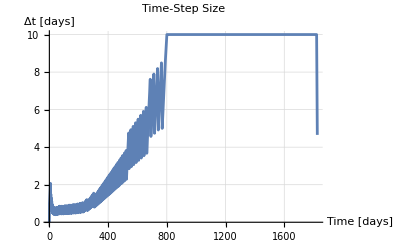

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

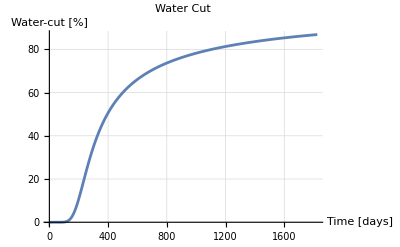

```mathematica
postProcess[t,x,dx]
```